```mathematica
f[x_] := (1/2) * ((1+x) * Log[1+x] + (1-x)*Log[1-x]);
```

```mathematica
g := InverseFunction[f];
```

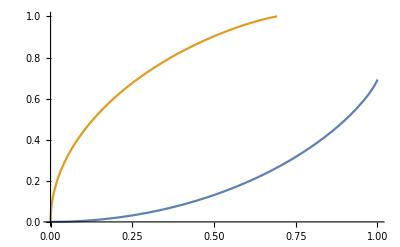

```mathematica
Plot[{f[x], g[x]}, {x, 0, 1}]
```

```mathematica
num= 10^50;
```

```mathematica
logN = N[Log[num]]
```

115.129

```mathematica
logspace[a_,b_,n_]:=Exp[Range[a,b,(b-a)/(n-1)]]
```

```mathematica
times = Subdivide[N[Log[num]]+1, 10^5, 5000]
```

{116.129,136.106,156.083,176.06,196.036,216.013,235.99,255.967,275.943,295.92,315.897,335.874,355.851,375.827,395.804,415.781,435.758,455.734,475.711,495.688,515.665,535.642,555.618,575.595,595.572,615.549,635.525,655.502,675.479,695.456,715.432,735.409,755.386,775.363,795.34,815.316,835.293,855.27,875.247,895.223,915.2,935.177,955.154,975.131,995.107,1015.08,1035.06,1055.04,1075.01,1094.99,1114.97,1134.94,1154.92,1174.9,1194.88,1214.85,1234.83,1254.81,1274.78,1294.76,1314.74,1334.71,1354.69,1374.67,1394.64,1414.62,1434.6,1454.57,1474.55,1494.53,1514.5,1534.48,1554.46,1574.43,1594.41,1614.39,1634.36,1654.34,1674.32,1694.29,1714.27,1734.25,1754.22,1774.2,1794.18,1814.16,1834.13,1854.11,1874.09,1894.06,1914.04,1934.02,1953.99,1973.97,1993.95,2013.92,2033.9,2053.88,2073.85,2093.83,2113.81,2133.78,2153.76,2173.74,2193.71,2213.69,2233.67,2253.64,2273.62,2293.6,2313.57,2333.55,2353.53,2373.5,2393.48,2413.46,2433.44,2453.41,2473.39,2493.37,2513.34,2533.32,2553.3,2573.27,2593.25,2613.23,2633.2,2653.18,2673.16,2693.13,2713.11,2733.09,2753.06,2773.04,2793.02,2812.99,2832.97,2852.95,2872.92,2892.9,2912.88,2932.85,2952.83,2972.81,2992.78,3012.76,3032.74,3052.72,3072.69,3092.67,3112.65,3132.62,3152.6,3172.58,3192.55,3212.53,3232.51,3252.48,3272.46,3292.44,3312.41,3332.39,3352.37,3372.34,3392.32,3412.3,3432.27,3452.25,3472.23,3492.2,3512.18,3532.16,3552.13,3572.11,3592.09,3612.06,3632.04,3652.02,3672.,3691.97,3711.95,3731.93,3751.9,3771.88,3791.86,3811.83,3831.81,3851.79,3871.76,3891.74,3911.72,3931.69,3951.67,3971.65,3991.62,4011.6,4031.58,4051.55,4071.53,4091.51,4111.48,4131.46,4151.44,4171.41,4191.39,4211.37,4231.34,4251.32,4271.3,4291.28,4311.25,4331.23,4351.21,4371.18,4391.16,4411.14,4431.11,4451.09,4471.07,4491.04,4511.02,4531.,4550.97,4570.95,4590.93,4610.9,4630.88,4650.86,4670.83,4690.81,4710.79,4730.76,4750.74,4770.72,4790.69,4810.67,4830.65,4850.62,4870.6,4890.58,4910.56,4930.53,4950.51,4970.49,4990.46,5010.44,5030.42,5050.39,5070.37,5090.35,5110.32,5130.3,5150.28,5170.25,5190.23,5210.21,5230.18,5250.16,5270.14,5290.11,5310.09,5330.07,5350.04,5370.02,5390.,5409.97,5429.95,5449.93,5469.9,5489.88,5509.86,5529.84,5549.81,5569.79,5589.77,5609.74,5629.72,5649.7,5669.67,5689.65,5709.63,5729.6,5749.58,5769.56,5789.53,5809.51,5829.49,5849.46,5869.44,5889.42,5909.39,5929.37,5949.35,5969.32,5989.3,6009.28,6029.25,6049.23,6069.21,6089.18,6109.16,6129.14,6149.12,6169.09,6189.07,6209.05,6229.02,6249.,6268.98,6288.95,6308.93,6328.91,6348.88,6368.86,6388.84,6408.81,6428.79,6448.77,6468.74,6488.72,6508.7,6528.67,6548.65,6568.63,6588.6,6608.58,6628.56,6648.53,6668.51,6688.49,6708.46,6728.44,6748.42,6768.4,6788.37,6808.35,6828.33,6848.3,6868.28,6888.26,6908.23,6928.21,6948.19,6968.16,6988.14,7008.12,7028.09,7048.07,7068.05,7088.02,7108.,7127.98,7147.95,7167.93,7187.91,7207.88,7227.86,7247.84,7267.81,7287.79,7307.77,7327.74,7347.72,7367.7,7387.68,7407.65,7427.63,7447.61,7467.58,7487.56,7507.54,7527.51,7547.49,7567.47,7587.44,7607.42,7627.4,7647.37,7667.35,7687.33,7707.3,7727.28,7747.26,7767.23,7787.21,7807.19,7827.16,7847.14,7867.12,7887.09,7907.07,7927.05,7947.02,7967.,7986.98,8006.96,8026.93,8046.91,8066.89,8086.86,8106.84,8126.82,8146.79,8166.77,8186.75,8206.72,8226.7,8246.68,8266.65,8286.63,8306.61,8326.58,8346.56,8366.54,8386.51,8406.49,8426.47,8446.44,8466.42,8486.4,8506.37,8526.35,8546.33,8566.3,8586.28,8606.26,8626.24,8646.21,8666.19,8686.17,8706.14,8726.12,8746.1,8766.07,8786.05,8806.03,8826.,8845.98,8865.96,8885.93,8905.91,8925.89,8945.86,8965.84,8985.82,9005.79,9025.77,9045.75,9065.72,9085.7,9105.68,9125.65,9145.63,9165.61,9185.58,9205.56,9225.54,9245.52,9265.49,9285.47,9305.45,9325.42,9345.4,9365.38,9385.35,9405.33,9425.31,9445.28,9465.26,9485.24,9505.21,9525.19,9545.17,9565.14,9585.12,9605.1,9625.07,9645.05,9665.03,9685.,9704.98,9724.96,9744.93,9764.91,9784.89,9804.86,9824.84,9844.82,9864.8,9884.77,9904.75,9924.73,9944.7,9964.68,9984.66,10004.6,10024.6,10044.6,10064.6,10084.5,10104.5,10124.5,10144.5,10164.4,10184.4,10204.4,10224.4,10244.4,10264.3,10284.3,10304.3,10324.3,10344.2,10364.2,10384.2,10404.2,10424.1,10444.1,10464.1,10484.1,10504.1,10524.,10544.,10564.,10584.,10603.9,10623.9,10643.9,10663.9,10683.8,10703.8,10723.8,10743.8,10763.7,10783.7,10803.7,10823.7,10843.7,10863.6,10883.6,10903.6,10923.6,10943.5,10963.5,10983.5,11003.5,11023.4,11043.4,11063.4,11083.4,11103.4,11123.3,11143.3,11163.3,11183.3,11203.2,11223.2,11243.2,11263.2,11283.1,11303.1,11323.1,11343.1,11363.1,11383.,11403.,11423.,11443.,11462.9,11482.9,11502.9,11522.9,11542.8,11562.8,11582.8,11602.8,11622.8,11642.7,11662.7,11682.7,11702.7,11722.6,11742.6,11762.6,11782.6,11802.5,11822.5,11842.5,11862.5,11882.4,11902.4,11922.4,11942.4,11962.4,11982.3,12002.3,12022.3,12042.3,12062.2,12082.2,12102.2,12122.2,12142.1,12162.1,12182.1,12202.1,12222.1,12242.,12262.,12282.,12302.,12321.9,12341.9,12361.9,12381.9,12401.8,12421.8,12441.8,12461.8,12481.8,12501.7,12521.7,12541.7,12561.7,12581.6,12601.6,12621.6,12641.6,12661.5,12681.5,12701.5,12721.5,12741.5,12761.4,12781.4,12801.4,12821.4,12841.3,12861.3,12881.3,12901.3,12921.2,12941.2,12961.2,12981.2,13001.1,13021.1,13041.1,13061.1,13081.1,13101.,13121.,13141.,13161.,13180.9,13200.9,13220.9,13240.9,13260.8,13280.8,13300.8,13320.8,13340.8,13360.7,13380.7,13400.7,13420.7,13440.6,13460.6,13480.6,13500.6,13520.5,13540.5,13560.5,13580.5,13600.5,13620.4,13640.4,13660.4,13680.4,13700.3,13720.3,13740.3,13760.3,13780.2,13800.2,13820.2,13840.2,13860.1,13880.1,13900.1,13920.1,13940.1,13960.,13980.,14000.,14020.,14039.9,14059.9,14079.9,14099.9,14119.8,14139.8,14159.8,14179.8,14199.8,14219.7,14239.7,14259.7,14279.7,14299.6,14319.6,14339.6,14359.6,14379.5,14399.5,14419.5,14439.5,14459.5,14479.4,14499.4,14519.4,14539.4,14559.3,14579.3,14599.3,14619.3,14639.2,14659.2,14679.2,14699.2,14719.2,14739.1,14759.1,14779.1,14799.1,14819.,14839.,14859.,14879.,14898.9,14918.9,14938.9,14958.9,14978.8,14998.8,15018.8,15038.8,15058.8,15078.7,15098.7,15118.7,15138.7,15158.6,15178.6,15198.6,15218.6,15238.5,15258.5,15278.5,15298.5,15318.5,15338.4,15358.4,15378.4,15398.4,15418.3,15438.3,15458.3,15478.3,15498.2,15518.2,15538.2,15558.2,15578.2,15598.1,15618.1,15638.1,15658.1,15678.,15698.,15718.,15738.,15757.9,15777.9,15797.9,15817.9,15837.9,15857.8,15877.8,15897.8,15917.8,15937.7,15957.7,15977.7,15997.7,16017.6,16037.6,16057.6,16077.6,16097.5,16117.5,16137.5,16157.5,16177.5,16197.4,16217.4,16237.4,16257.4,16277.3,16297.3,16317.3,16337.3,16357.2,16377.2,16397.2,16417.2,16437.2,16457.1,16477.1,16497.1,16517.1,16537.,16557.,16577.,16597.,16616.9,16636.9,16656.9,16676.9,16696.9,16716.8,16736.8,16756.8,16776.8,16796.7,16816.7,16836.7,16856.7,16876.6,16896.6,16916.6,16936.6,16956.5,16976.5,16996.5,17016.5,17036.5,17056.4,17076.4,17096.4,17116.4,17136.3,17156.3,17176.3,17196.3,17216.2,17236.2,17256.2,17276.2,17296.2,17316.1,17336.1,17356.1,17376.1,17396.,17416.,17436.,17456.,17475.9,17495.9,17515.9,17535.9,17555.9,17575.8,17595.8,17615.8,17635.8,17655.7,17675.7,17695.7,17715.7,17735.6,17755.6,17775.6,17795.6,17815.6,17835.5,17855.5,17875.5,17895.5,17915.4,17935.4,17955.4,17975.4,17995.3,18015.3,18035.3,18055.3,18075.2,18095.2,18115.2,18135.2,18155.2,18175.1,18195.1,18215.1,18235.1,18255.,18275.,18295.,18315.,18334.9,18354.9,18374.9,18394.9,18414.9,18434.8,18454.8,18474.8,18494.8,18514.7,18534.7,18554.7,18574.7,18594.6,18614.6,18634.6,18654.6,18674.6,18694.5,18714.5,18734.5,18754.5,18774.4,18794.4,18814.4,18834.4,18854.3,18874.3,18894.3,18914.3,18934.3,18954.2,18974.2,18994.2,19014.2,19034.1,19054.1,19074.1,19094.1,19114.,19134.,19154.,19174.,19193.9,19213.9,19233.9,19253.9,19273.9,19293.8,19313.8,19333.8,19353.8,19373.7,19393.7,19413.7,19433.7,19453.6,19473.6,19493.6,19513.6,19533.6,19553.5,19573.5,19593.5,19613.5,19633.4,19653.4,19673.4,19693.4,19713.3,19733.3,19753.3,19773.3,19793.3,19813.2,19833.2,19853.2,19873.2,19893.1,19913.1,19933.1,19953.1,19973.,19993.,20013.,20033.,20052.9,20072.9,20092.9,20112.9,20132.9,20152.8,20172.8,20192.8,20212.8,20232.7,20252.7,20272.7,20292.7,20312.6,20332.6,20352.6,20372.6,20392.6,20412.5,20432.5,20452.5,20472.5,20492.4,20512.4,20532.4,20552.4,20572.3,20592.3,20612.3,20632.3,20652.3,20672.2,20692.2,20712.2,20732.2,20752.1,20772.1,20792.1,20812.1,20832.,20852.,20872.,20892.,20912.,20931.9,20951.9,20971.9,20991.9,21011.8,21031.8,21051.8,21071.8,21091.7,21111.7,21131.7,21151.7,21171.6,21191.6,21211.6,21231.6,21251.6,21271.5,21291.5,21311.5,21331.5,21351.4,21371.4,21391.4,21411.4,21431.3,21451.3,21471.3,21491.3,21511.3,21531.2,21551.2,21571.2,21591.2,21611.1,21631.1,21651.1,21671.1,21691.,21711.,21731.,21751.,21771.,21790.9,21810.9,21830.9,21850.9,21870.8,21890.8,21910.8,21930.8,21950.7,21970.7,21990.7,22010.7,22030.7,22050.6,22070.6,22090.6,22110.6,22130.5,22150.5,22170.5,22190.5,22210.4,22230.4,22250.4,22270.4,22290.3,22310.3,22330.3,22350.3,22370.3,22390.2,22410.2,22430.2,22450.2,22470.1,22490.1,22510.1,22530.1,22550.,22570.,22590.,22610.,22630.,22649.9,22669.9,22689.9,22709.9,22729.8,22749.8,22769.8,22789.8,22809.7,22829.7,22849.7,22869.7,22889.7,22909.6,22929.6,22949.6,22969.6,22989.5,23009.5,23029.5,23049.5,23069.4,23089.4,23109.4,23129.4,23149.3,23169.3,23189.3,23209.3,23229.3,23249.2,23269.2,23289.2,23309.2,23329.1,23349.1,23369.1,23389.1,23409.,23429.,23449.,23469.,23489.,23508.9,23528.9,23548.9,23568.9,23588.8,23608.8,23628.8,23648.8,23668.7,23688.7,23708.7,23728.7,23748.7,23768.6,23788.6,23808.6,23828.6,23848.5,23868.5,23888.5,23908.5,23928.4,23948.4,23968.4,23988.4,24008.4,24028.3,24048.3,24068.3,24088.3,24108.2,24128.2,24148.2,24168.2,24188.1,24208.1,24228.1,24248.1,24268.,24288.,24308.,24328.,24348.,24367.9,24387.9,24407.9,24427.9,24447.8,24467.8,24487.8,24507.8,24527.7,24547.7,24567.7,24587.7,24607.7,24627.6,24647.6,24667.6,24687.6,24707.5,24727.5,24747.5,24767.5,24787.4,24807.4,24827.4,24847.4,24867.4,24887.3,24907.3,24927.3,24947.3,24967.2,24987.2,25007.2,25027.2,25047.1,25067.1,25087.1,25107.1,25127.1,25147.,25167.,25187.,25207.,25226.9,25246.9,25266.9,25286.9,25306.8,25326.8,25346.8,25366.8,25386.7,25406.7,25426.7,25446.7,25466.7,25486.6,25506.6,25526.6,25546.6,25566.5,25586.5,25606.5,25626.5,25646.4,25666.4,25686.4,25706.4,25726.4,25746.3,25766.3,25786.3,25806.3,25826.2,25846.2,25866.2,25886.2,25906.1,25926.1,25946.1,25966.1,25986.1,26006.,26026.,26046.,26066.,26085.9,26105.9,26125.9,26145.9,26165.8,26185.8,26205.8,26225.8,26245.7,26265.7,26285.7,26305.7,26325.7,26345.6,26365.6,26385.6,26405.6,26425.5,26445.5,26465.5,26485.5,26505.4,26525.4,26545.4,26565.4,26585.4,26605.3,26625.3,26645.3,26665.3,26685.2,26705.2,26725.2,26745.2,26765.1,26785.1,26805.1,26825.1,26845.1,26865.,26885.,26905.,26925.,26944.9,26964.9,26984.9,27004.9,27024.8,27044.8,27064.8,27084.8,27104.8,27124.7,27144.7,27164.7,27184.7,27204.6,27224.6,27244.6,27264.6,27284.5,27304.5,27324.5,27344.5,27364.4,27384.4,27404.4,27424.4,27444.4,27464.3,27484.3,27504.3,27524.3,27544.2,27564.2,27584.2,27604.2,27624.1,27644.1,27664.1,27684.1,27704.1,27724.,27744.,27764.,27784.,27803.9,27823.9,27843.9,27863.9,27883.8,27903.8,27923.8,27943.8,27963.8,27983.7,28003.7,28023.7,28043.7,28063.6,28083.6,28103.6,28123.6,28143.5,28163.5,28183.5,28203.5,28223.5,28243.4,28263.4,28283.4,28303.4,28323.3,28343.3,28363.3,28383.3,28403.2,28423.2,28443.2,28463.2,28483.1,28503.1,28523.1,28543.1,28563.1,28583.,28603.,28623.,28643.,28662.9,28682.9,28702.9,28722.9,28742.8,28762.8,28782.8,28802.8,28822.8,28842.7,28862.7,28882.7,28902.7,28922.6,28942.6,28962.6,28982.6,29002.5,29022.5,29042.5,29062.5,29082.5,29102.4,29122.4,29142.4,29162.4,29182.3,29202.3,29222.3,29242.3,29262.2,29282.2,29302.2,29322.2,29342.1,29362.1,29382.1,29402.1,29422.1,29442.,29462.,29482.,29502.,29521.9,29541.9,29561.9,29581.9,29601.8,29621.8,29641.8,29661.8,29681.8,29701.7,29721.7,29741.7,29761.7,29781.6,29801.6,29821.6,29841.6,29861.5,29881.5,29901.5,29921.5,29941.5,29961.4,29981.4,30001.4,30021.4,30041.3,30061.3,30081.3,30101.3,30121.2,30141.2,30161.2,30181.2,30201.2,30221.1,30241.1,30261.1,30281.1,30301.,30321.,30341.,30361.,30380.9,30400.9,30420.9,30440.9,30460.8,30480.8,30500.8,30520.8,30540.8,30560.7,30580.7,30600.7,30620.7,30640.6,30660.6,30680.6,30700.6,30720.5,30740.5,30760.5,30780.5,30800.5,30820.4,30840.4,30860.4,30880.4,30900.3,30920.3,30940.3,30960.3,30980.2,31000.2,31020.2,31040.2,31060.2,31080.1,31100.1,31120.1,31140.1,31160.,31180.,31200.,31220.,31239.9,31259.9,31279.9,31299.9,31319.9,31339.8,31359.8,31379.8,31399.8,31419.7,31439.7,31459.7,31479.7,31499.6,31519.6,31539.6,31559.6,31579.5,31599.5,31619.5,31639.5,31659.5,31679.4,31699.4,31719.4,31739.4,31759.3,31779.3,31799.3,31819.3,31839.2,31859.2,31879.2,31899.2,31919.2,31939.1,31959.1,31979.1,31999.1,32019.,32039.,32059.,32079.,32098.9,32118.9,32138.9,32158.9,32178.9,32198.8,32218.8,32238.8,32258.8,32278.7,32298.7,32318.7,32338.7,32358.6,32378.6,32398.6,32418.6,32438.5,32458.5,32478.5,32498.5,32518.5,32538.4,32558.4,32578.4,32598.4,32618.3,32638.3,32658.3,32678.3,32698.2,32718.2,32738.2,32758.2,32778.2,32798.1,32818.1,32838.1,32858.1,32878.,32898.,32918.,32938.,32957.9,32977.9,32997.9,33017.9,33037.9,33057.8,33077.8,33097.8,33117.8,33137.7,33157.7,33177.7,33197.7,33217.6,33237.6,33257.6,33277.6,33297.6,33317.5,33337.5,33357.5,33377.5,33397.4,33417.4,33437.4,33457.4,33477.3,33497.3,33517.3,33537.3,33557.2,33577.2,33597.2,33617.2,33637.2,33657.1,33677.1,33697.1,33717.1,33737.,33757.,33777.,33797.,33816.9,33836.9,33856.9,33876.9,33896.9,33916.8,33936.8,33956.8,33976.8,33996.7,34016.7,34036.7,34056.7,34076.6,34096.6,34116.6,34136.6,34156.6,34176.5,34196.5,34216.5,34236.5,34256.4,34276.4,34296.4,34316.4,34336.3,34356.3,34376.3,34396.3,34416.3,34436.2,34456.2,34476.2,34496.2,34516.1,34536.1,34556.1,34576.1,34596.,34616.,34636.,34656.,34675.9,34695.9,34715.9,34735.9,34755.9,34775.8,34795.8,34815.8,34835.8,34855.7,34875.7,34895.7,34915.7,34935.6,34955.6,34975.6,34995.6,35015.6,35035.5,35055.5,35075.5,35095.5,35115.4,35135.4,35155.4,35175.4,35195.3,35215.3,35235.3,35255.3,35275.3,35295.2,35315.2,35335.2,35355.2,35375.1,35395.1,35415.1,35435.1,35455.,35475.,35495.,35515.,35534.9,35554.9,35574.9,35594.9,35614.9,35634.8,35654.8,35674.8,35694.8,35714.7,35734.7,35754.7,35774.7,35794.6,35814.6,35834.6,35854.6,35874.6,35894.5,35914.5,35934.5,35954.5,35974.4,35994.4,36014.4,36034.4,36054.3,36074.3,36094.3,36114.3,36134.3,36154.2,36174.2,36194.2,36214.2,36234.1,36254.1,36274.1,36294.1,36314.,36334.,36354.,36374.,36394.,36413.9,36433.9,36453.9,36473.9,36493.8,36513.8,36533.8,36553.8,36573.7,36593.7,36613.7,36633.7,36653.6,36673.6,36693.6,36713.6,36733.6,36753.5,36773.5,36793.5,36813.5,36833.4,36853.4,36873.4,36893.4,36913.3,36933.3,36953.3,36973.3,36993.3,37013.2,37033.2,37053.2,37073.2,37093.1,37113.1,37133.1,37153.1,37173.,37193.,37213.,37233.,37253.,37272.9,37292.9,37312.9,37332.9,37352.8,37372.8,37392.8,37412.8,37432.7,37452.7,37472.7,37492.7,37512.7,37532.6,37552.6,37572.6,37592.6,37612.5,37632.5,37652.5,37672.5,37692.4,37712.4,37732.4,37752.4,37772.3,37792.3,37812.3,37832.3,37852.3,37872.2,37892.2,37912.2,37932.2,37952.1,37972.1,37992.1,38012.1,38032.,38052.,38072.,38092.,38112.,38131.9,38151.9,38171.9,38191.9,38211.8,38231.8,38251.8,38271.8,38291.7,38311.7,38331.7,38351.7,38371.7,38391.6,38411.6,38431.6,38451.6,38471.5,38491.5,38511.5,38531.5,38551.4,38571.4,38591.4,38611.4,38631.3,38651.3,38671.3,38691.3,38711.3,38731.2,38751.2,38771.2,38791.2,38811.1,38831.1,38851.1,38871.1,38891.,38911.,38931.,38951.,38971.,38990.9,39010.9,39030.9,39050.9,39070.8,39090.8,39110.8,39130.8,39150.7,39170.7,39190.7,39210.7,39230.7,39250.6,39270.6,39290.6,39310.6,39330.5,39350.5,39370.5,39390.5,39410.4,39430.4,39450.4,39470.4,39490.4,39510.3,39530.3,39550.3,39570.3,39590.2,39610.2,39630.2,39650.2,39670.1,39690.1,39710.1,39730.1,39750.,39770.,39790.,39810.,39830.,39849.9,39869.9,39889.9,39909.9,39929.8,39949.8,39969.8,39989.8,40009.7,40029.7,40049.7,40069.7,40089.7,40109.6,40129.6,40149.6,40169.6,40189.5,40209.5,40229.5,40249.5,40269.4,40289.4,40309.4,40329.4,40349.4,40369.3,40389.3,40409.3,40429.3,40449.2,40469.2,40489.2,40509.2,40529.1,40549.1,40569.1,40589.1,40609.1,40629.,40649.,40669.,40689.,40708.9,40728.9,40748.9,40768.9,40788.8,40808.8,40828.8,40848.8,40868.7,40888.7,40908.7,40928.7,40948.7,40968.6,40988.6,41008.6,41028.6,41048.5,41068.5,41088.5,41108.5,41128.4,41148.4,41168.4,41188.4,41208.4,41228.3,41248.3,41268.3,41288.3,41308.2,41328.2,41348.2,41368.2,41388.1,41408.1,41428.1,41448.1,41468.1,41488.,41508.,41528.,41548.,41567.9,41587.9,41607.9,41627.9,41647.8,41667.8,41687.8,41707.8,41727.7,41747.7,41767.7,41787.7,41807.7,41827.6,41847.6,41867.6,41887.6,41907.5,41927.5,41947.5,41967.5,41987.4,42007.4,42027.4,42047.4,42067.4,42087.3,42107.3,42127.3,42147.3,42167.2,42187.2,42207.2,42227.2,42247.1,42267.1,42287.1,42307.1,42327.1,42347.,42367.,42387.,42407.,42426.9,42446.9,42466.9,42486.9,42506.8,42526.8,42546.8,42566.8,42586.8,42606.7,42626.7,42646.7,42666.7,42686.6,42706.6,42726.6,42746.6,42766.5,42786.5,42806.5,42826.5,42846.4,42866.4,42886.4,42906.4,42926.4,42946.3,42966.3,42986.3,43006.3,43026.2,43046.2,43066.2,43086.2,43106.1,43126.1,43146.1,43166.1,43186.1,43206.,43226.,43246.,43266.,43285.9,43305.9,43325.9,43345.9,43365.8,43385.8,43405.8,43425.8,43445.8,43465.7,43485.7,43505.7,43525.7,43545.6,43565.6,43585.6,43605.6,43625.5,43645.5,43665.5,43685.5,43705.5,43725.4,43745.4,43765.4,43785.4,43805.3,43825.3,43845.3,43865.3,43885.2,43905.2,43925.2,43945.2,43965.1,43985.1,44005.1,44025.1,44045.1,44065.,44085.,44105.,44125.,44144.9,44164.9,44184.9,44204.9,44224.8,44244.8,44264.8,44284.8,44304.8,44324.7,44344.7,44364.7,44384.7,44404.6,44424.6,44444.6,44464.6,44484.5,44504.5,44524.5,44544.5,44564.5,44584.4,44604.4,44624.4,44644.4,44664.3,44684.3,44704.3,44724.3,44744.2,44764.2,44784.2,44804.2,44824.1,44844.1,44864.1,44884.1,44904.1,44924.,44944.,44964.,44984.,45003.9,45023.9,45043.9,45063.9,45083.8,45103.8,45123.8,45143.8,45163.8,45183.7,45203.7,45223.7,45243.7,45263.6,45283.6,45303.6,45323.6,45343.5,45363.5,45383.5,45403.5,45423.5,45443.4,45463.4,45483.4,45503.4,45523.3,45543.3,45563.3,45583.3,45603.2,45623.2,45643.2,45663.2,45683.2,45703.1,45723.1,45743.1,45763.1,45783.,45803.,45823.,45843.,45862.9,45882.9,45902.9,45922.9,45942.8,45962.8,45982.8,46002.8,46022.8,46042.7,46062.7,46082.7,46102.7,46122.6,46142.6,46162.6,46182.6,46202.5,46222.5,46242.5,46262.5,46282.5,46302.4,46322.4,46342.4,46362.4,46382.3,46402.3,46422.3,46442.3,46462.2,46482.2,46502.2,46522.2,46542.2,46562.1,46582.1,46602.1,46622.1,46642.,46662.,46682.,46702.,46721.9,46741.9,46761.9,46781.9,46801.9,46821.8,46841.8,46861.8,46881.8,46901.7,46921.7,46941.7,46961.7,46981.6,47001.6,47021.6,47041.6,47061.5,47081.5,47101.5,47121.5,47141.5,47161.4,47181.4,47201.4,47221.4,47241.3,47261.3,47281.3,47301.3,47321.2,47341.2,47361.2,47381.2,47401.2,47421.1,47441.1,47461.1,47481.1,47501.,47521.,47541.,47561.,47580.9,47600.9,47620.9,47640.9,47660.9,47680.8,47700.8,47720.8,47740.8,47760.7,47780.7,47800.7,47820.7,47840.6,47860.6,47880.6,47900.6,47920.5,47940.5,47960.5,47980.5,48000.5,48020.4,48040.4,48060.4,48080.4,48100.3,48120.3,48140.3,48160.3,48180.2,48200.2,48220.2,48240.2,48260.2,48280.1,48300.1,48320.1,48340.1,48360.,48380.,48400.,48420.,48439.9,48459.9,48479.9,48499.9,48519.9,48539.8,48559.8,48579.8,48599.8,48619.7,48639.7,48659.7,48679.7,48699.6,48719.6,48739.6,48759.6,48779.6,48799.5,48819.5,48839.5,48859.5,48879.4,48899.4,48919.4,48939.4,48959.3,48979.3,48999.3,49019.3,49039.2,49059.2,49079.2,49099.2,49119.2,49139.1,49159.1,49179.1,49199.1,49219.,49239.,49259.,49279.,49298.9,49318.9,49338.9,49358.9,49378.9,49398.8,49418.8,49438.8,49458.8,49478.7,49498.7,49518.7,49538.7,49558.6,49578.6,49598.6,49618.6,49638.6,49658.5,49678.5,49698.5,49718.5,49738.4,49758.4,49778.4,49798.4,49818.3,49838.3,49858.3,49878.3,49898.3,49918.2,49938.2,49958.2,49978.2,49998.1,50018.1,50038.1,50058.1,50078.,50098.,50118.,50138.,50157.9,50177.9,50197.9,50217.9,50237.9,50257.8,50277.8,50297.8,50317.8,50337.7,50357.7,50377.7,50397.7,50417.6,50437.6,50457.6,50477.6,50497.6,50517.5,50537.5,50557.5,50577.5,50597.4,50617.4,50637.4,50657.4,50677.3,50697.3,50717.3,50737.3,50757.3,50777.2,50797.2,50817.2,50837.2,50857.1,50877.1,50897.1,50917.1,50937.,50957.,50977.,50997.,51016.9,51036.9,51056.9,51076.9,51096.9,51116.8,51136.8,51156.8,51176.8,51196.7,51216.7,51236.7,51256.7,51276.6,51296.6,51316.6,51336.6,51356.6,51376.5,51396.5,51416.5,51436.5,51456.4,51476.4,51496.4,51516.4,51536.3,51556.3,51576.3,51596.3,51616.3,51636.2,51656.2,51676.2,51696.2,51716.1,51736.1,51756.1,51776.1,51796.,51816.,51836.,51856.,51876.,51895.9,51915.9,51935.9,51955.9,51975.8,51995.8,52015.8,52035.8,52055.7,52075.7,52095.7,52115.7,52135.6,52155.6,52175.6,52195.6,52215.6,52235.5,52255.5,52275.5,52295.5,52315.4,52335.4,52355.4,52375.4,52395.3,52415.3,52435.3,52455.3,52475.3,52495.2,52515.2,52535.2,52555.2,52575.1,52595.1,52615.1,52635.1,52655.,52675.,52695.,52715.,52735.,52754.9,52774.9,52794.9,52814.9,52834.8,52854.8,52874.8,52894.8,52914.7,52934.7,52954.7,52974.7,52994.7,53014.6,53034.6,53054.6,53074.6,53094.5,53114.5,53134.5,53154.5,53174.4,53194.4,53214.4,53234.4,53254.3,53274.3,53294.3,53314.3,53334.3,53354.2,53374.2,53394.2,53414.2,53434.1,53454.1,53474.1,53494.1,53514.,53534.,53554.,53574.,53594.,53613.9,53633.9,53653.9,53673.9,53693.8,53713.8,53733.8,53753.8,53773.7,53793.7,53813.7,53833.7,53853.7,53873.6,53893.6,53913.6,53933.6,53953.5,53973.5,53993.5,54013.5,54033.4,54053.4,54073.4,54093.4,54113.3,54133.3,54153.3,54173.3,54193.3,54213.2,54233.2,54253.2,54273.2,54293.1,54313.1,54333.1,54353.1,54373.,54393.,54413.,54433.,54453.,54472.9,54492.9,54512.9,54532.9,54552.8,54572.8,54592.8,54612.8,54632.7,54652.7,54672.7,54692.7,54712.7,54732.6,54752.6,54772.6,54792.6,54812.5,54832.5,54852.5,54872.5,54892.4,54912.4,54932.4,54952.4,54972.4,54992.3,55012.3,55032.3,55052.3,55072.2,55092.2,55112.2,55132.2,55152.1,55172.1,55192.1,55212.1,55232.,55252.,55272.,55292.,55312.,55331.9,55351.9,55371.9,55391.9,55411.8,55431.8,55451.8,55471.8,55491.7,55511.7,55531.7,55551.7,55571.7,55591.6,55611.6,55631.6,55651.6,55671.5,55691.5,55711.5,55731.5,55751.4,55771.4,55791.4,55811.4,55831.4,55851.3,55871.3,55891.3,55911.3,55931.2,55951.2,55971.2,55991.2,56011.1,56031.1,56051.1,56071.1,56091.1,56111.,56131.,56151.,56171.,56190.9,56210.9,56230.9,56250.9,56270.8,56290.8,56310.8,56330.8,56350.7,56370.7,56390.7,56410.7,56430.7,56450.6,56470.6,56490.6,56510.6,56530.5,56550.5,56570.5,56590.5,56610.4,56630.4,56650.4,56670.4,56690.4,56710.3,56730.3,56750.3,56770.3,56790.2,56810.2,56830.2,56850.2,56870.1,56890.1,56910.1,56930.1,56950.1,56970.,56990.,57010.,57030.,57049.9,57069.9,57089.9,57109.9,57129.8,57149.8,57169.8,57189.8,57209.7,57229.7,57249.7,57269.7,57289.7,57309.6,57329.6,57349.6,57369.6,57389.5,57409.5,57429.5,57449.5,57469.4,57489.4,57509.4,57529.4,57549.4,57569.3,57589.3,57609.3,57629.3,57649.2,57669.2,57689.2,57709.2,57729.1,57749.1,57769.1,57789.1,57809.1,57829.,57849.,57869.,57889.,57908.9,57928.9,57948.9,57968.9,57988.8,58008.8,58028.8,58048.8,58068.8,58088.7,58108.7,58128.7,58148.7,58168.6,58188.6,58208.6,58228.6,58248.5,58268.5,58288.5,58308.5,58328.4,58348.4,58368.4,58388.4,58408.4,58428.3,58448.3,58468.3,58488.3,58508.2,58528.2,58548.2,58568.2,58588.1,58608.1,58628.1,58648.1,58668.1,58688.,58708.,58728.,58748.,58767.9,58787.9,58807.9,58827.9,58847.8,58867.8,58887.8,58907.8,58927.8,58947.7,58967.7,58987.7,59007.7,59027.6,59047.6,59067.6,59087.6,59107.5,59127.5,59147.5,59167.5,59187.5,59207.4,59227.4,59247.4,59267.4,59287.3,59307.3,59327.3,59347.3,59367.2,59387.2,59407.2,59427.2,59447.1,59467.1,59487.1,59507.1,59527.1,59547.,59567.,59587.,59607.,59626.9,59646.9,59666.9,59686.9,59706.8,59726.8,59746.8,59766.8,59786.8,59806.7,59826.7,59846.7,59866.7,59886.6,59906.6,59926.6,59946.6,59966.5,59986.5,60006.5,60026.5,60046.5,60066.4,60086.4,60106.4,60126.4,60146.3,60166.3,60186.3,60206.3,60226.2,60246.2,60266.2,60286.2,60306.1,60326.1,60346.1,60366.1,60386.1,60406.,60426.,60446.,60466.,60485.9,60505.9,60525.9,60545.9,60565.8,60585.8,60605.8,60625.8,60645.8,60665.7,60685.7,60705.7,60725.7,60745.6,60765.6,60785.6,60805.6,60825.5,60845.5,60865.5,60885.5,60905.5,60925.4,60945.4,60965.4,60985.4,61005.3,61025.3,61045.3,61065.3,61085.2,61105.2,61125.2,61145.2,61165.2,61185.1,61205.1,61225.1,61245.1,61265.,61285.,61305.,61325.,61344.9,61364.9,61384.9,61404.9,61424.8,61444.8,61464.8,61484.8,61504.8,61524.7,61544.7,61564.7,61584.7,61604.6,61624.6,61644.6,61664.6,61684.5,61704.5,61724.5,61744.5,61764.5,61784.4,61804.4,61824.4,61844.4,61864.3,61884.3,61904.3,61924.3,61944.2,61964.2,61984.2,62004.2,62024.2,62044.1,62064.1,62084.1,62104.1,62124.,62144.,62164.,62184.,62203.9,62223.9,62243.9,62263.9,62283.9,62303.8,62323.8,62343.8,62363.8,62383.7,62403.7,62423.7,62443.7,62463.6,62483.6,62503.6,62523.6,62543.5,62563.5,62583.5,62603.5,62623.5,62643.4,62663.4,62683.4,62703.4,62723.3,62743.3,62763.3,62783.3,62803.2,62823.2,62843.2,62863.2,62883.2,62903.1,62923.1,62943.1,62963.1,62983.,63003.,63023.,63043.,63062.9,63082.9,63102.9,63122.9,63142.9,63162.8,63182.8,63202.8,63222.8,63242.7,63262.7,63282.7,63302.7,63322.6,63342.6,63362.6,63382.6,63402.5,63422.5,63442.5,63462.5,63482.5,63502.4,63522.4,63542.4,63562.4,63582.3,63602.3,63622.3,63642.3,63662.2,63682.2,63702.2,63722.2,63742.2,63762.1,63782.1,63802.1,63822.1,63842.,63862.,63882.,63902.,63921.9,63941.9,63961.9,63981.9,64001.9,64021.8,64041.8,64061.8,64081.8,64101.7,64121.7,64141.7,64161.7,64181.6,64201.6,64221.6,64241.6,64261.6,64281.5,64301.5,64321.5,64341.5,64361.4,64381.4,64401.4,64421.4,64441.3,64461.3,64481.3,64501.3,64521.2,64541.2,64561.2,64581.2,64601.2,64621.1,64641.1,64661.1,64681.1,64701.,64721.,64741.,64761.,64780.9,64800.9,64820.9,64840.9,64860.9,64880.8,64900.8,64920.8,64940.8,64960.7,64980.7,65000.7,65020.7,65040.6,65060.6,65080.6,65100.6,65120.6,65140.5,65160.5,65180.5,65200.5,65220.4,65240.4,65260.4,65280.4,65300.3,65320.3,65340.3,65360.3,65380.3,65400.2,65420.2,65440.2,65460.2,65480.1,65500.1,65520.1,65540.1,65560.,65580.,65600.,65620.,65639.9,65659.9,65679.9,65699.9,65719.9,65739.8,65759.8,65779.8,65799.8,65819.7,65839.7,65859.7,65879.7,65899.6,65919.6,65939.6,65959.6,65979.6,65999.5,66019.5,66039.5,66059.5,66079.4,66099.4,66119.4,66139.4,66159.3,66179.3,66199.3,66219.3,66239.3,66259.2,66279.2,66299.2,66319.2,66339.1,66359.1,66379.1,66399.1,66419.,66439.,66459.,66479.,66498.9,66518.9,66538.9,66558.9,66578.9,66598.8,66618.8,66638.8,66658.8,66678.7,66698.7,66718.7,66738.7,66758.6,66778.6,66798.6,66818.6,66838.6,66858.5,66878.5,66898.5,66918.5,66938.4,66958.4,66978.4,66998.4,67018.3,67038.3,67058.3,67078.3,67098.3,67118.2,67138.2,67158.2,67178.2,67198.1,67218.1,67238.1,67258.1,67278.,67298.,67318.,67338.,67358.,67377.9,67397.9,67417.9,67437.9,67457.8,67477.8,67497.8,67517.8,67537.7,67557.7,67577.7,67597.7,67617.6,67637.6,67657.6,67677.6,67697.6,67717.5,67737.5,67757.5,67777.5,67797.4,67817.4,67837.4,67857.4,67877.3,67897.3,67917.3,67937.3,67957.3,67977.2,67997.2,68017.2,68037.2,68057.1,68077.1,68097.1,68117.1,68137.,68157.,68177.,68197.,68217.,68236.9,68256.9,68276.9,68296.9,68316.8,68336.8,68356.8,68376.8,68396.7,68416.7,68436.7,68456.7,68476.7,68496.6,68516.6,68536.6,68556.6,68576.5,68596.5,68616.5,68636.5,68656.4,68676.4,68696.4,68716.4,68736.3,68756.3,68776.3,68796.3,68816.3,68836.2,68856.2,68876.2,68896.2,68916.1,68936.1,68956.1,68976.1,68996.,69016.,69036.,69056.,69076.,69095.9,69115.9,69135.9,69155.9,69175.8,69195.8,69215.8,69235.8,69255.7,69275.7,69295.7,69315.7,69335.7,69355.6,69375.6,69395.6,69415.6,69435.5,69455.5,69475.5,69495.5,69515.4,69535.4,69555.4,69575.4,69595.3,69615.3,69635.3,69655.3,69675.3,69695.2,69715.2,69735.2,69755.2,69775.1,69795.1,69815.1,69835.1,69855.,69875.,69895.,69915.,69935.,69954.9,69974.9,69994.9,70014.9,70034.8,70054.8,70074.8,70094.8,70114.7,70134.7,70154.7,70174.7,70194.7,70214.6,70234.6,70254.6,70274.6,70294.5,70314.5,70334.5,70354.5,70374.4,70394.4,70414.4,70434.4,70454.4,70474.3,70494.3,70514.3,70534.3,70554.2,70574.2,70594.2,70614.2,70634.1,70654.1,70674.1,70694.1,70714.,70734.,70754.,70774.,70794.,70813.9,70833.9,70853.9,70873.9,70893.8,70913.8,70933.8,70953.8,70973.7,70993.7,71013.7,71033.7,71053.7,71073.6,71093.6,71113.6,71133.6,71153.5,71173.5,71193.5,71213.5,71233.4,71253.4,71273.4,71293.4,71313.4,71333.3,71353.3,71373.3,71393.3,71413.2,71433.2,71453.2,71473.2,71493.1,71513.1,71533.1,71553.1,71573.1,71593.,71613.,71633.,71653.,71672.9,71692.9,71712.9,71732.9,71752.8,71772.8,71792.8,71812.8,71832.7,71852.7,71872.7,71892.7,71912.7,71932.6,71952.6,71972.6,71992.6,72012.5,72032.5,72052.5,72072.5,72092.4,72112.4,72132.4,72152.4,72172.4,72192.3,72212.3,72232.3,72252.3,72272.2,72292.2,72312.2,72332.2,72352.1,72372.1,72392.1,72412.1,72432.1,72452.,72472.,72492.,72512.,72531.9,72551.9,72571.9,72591.9,72611.8,72631.8,72651.8,72671.8,72691.7,72711.7,72731.7,72751.7,72771.7,72791.6,72811.6,72831.6,72851.6,72871.5,72891.5,72911.5,72931.5,72951.4,72971.4,72991.4,73011.4,73031.4,73051.3,73071.3,73091.3,73111.3,73131.2,73151.2,73171.2,73191.2,73211.1,73231.1,73251.1,73271.1,73291.1,73311.,73331.,73351.,73371.,73390.9,73410.9,73430.9,73450.9,73470.8,73490.8,73510.8,73530.8,73550.8,73570.7,73590.7,73610.7,73630.7,73650.6,73670.6,73690.6,73710.6,73730.5,73750.5,73770.5,73790.5,73810.4,73830.4,73850.4,73870.4,73890.4,73910.3,73930.3,73950.3,73970.3,73990.2,74010.2,74030.2,74050.2,74070.1,74090.1,74110.1,74130.1,74150.1,74170.,74190.,74210.,74230.,74249.9,74269.9,74289.9,74309.9,74329.8,74349.8,74369.8,74389.8,74409.8,74429.7,74449.7,74469.7,74489.7,74509.6,74529.6,74549.6,74569.6,74589.5,74609.5,74629.5,74649.5,74669.5,74689.4,74709.4,74729.4,74749.4,74769.3,74789.3,74809.3,74829.3,74849.2,74869.2,74889.2,74909.2,74929.1,74949.1,74969.1,74989.1,75009.1,75029.,75049.,75069.,75089.,75108.9,75128.9,75148.9,75168.9,75188.8,75208.8,75228.8,75248.8,75268.8,75288.7,75308.7,75328.7,75348.7,75368.6,75388.6,75408.6,75428.6,75448.5,75468.5,75488.5,75508.5,75528.5,75548.4,75568.4,75588.4,75608.4,75628.3,75648.3,75668.3,75688.3,75708.2,75728.2,75748.2,75768.2,75788.1,75808.1,75828.1,75848.1,75868.1,75888.,75908.,75928.,75948.,75967.9,75987.9,76007.9,76027.9,76047.8,76067.8,76087.8,76107.8,76127.8,76147.7,76167.7,76187.7,76207.7,76227.6,76247.6,76267.6,76287.6,76307.5,76327.5,76347.5,76367.5,76387.5,76407.4,76427.4,76447.4,76467.4,76487.3,76507.3,76527.3,76547.3,76567.2,76587.2,76607.2,76627.2,76647.2,76667.1,76687.1,76707.1,76727.1,76747.,76767.,76787.,76807.,76826.9,76846.9,76866.9,76886.9,76906.8,76926.8,76946.8,76966.8,76986.8,77006.7,77026.7,77046.7,77066.7,77086.6,77106.6,77126.6,77146.6,77166.5,77186.5,77206.5,77226.5,77246.5,77266.4,77286.4,77306.4,77326.4,77346.3,77366.3,77386.3,77406.3,77426.2,77446.2,77466.2,77486.2,77506.2,77526.1,77546.1,77566.1,77586.1,77606.,77626.,77646.,77666.,77685.9,77705.9,77725.9,77745.9,77765.9,77785.8,77805.8,77825.8,77845.8,77865.7,77885.7,77905.7,77925.7,77945.6,77965.6,77985.6,78005.6,78025.5,78045.5,78065.5,78085.5,78105.5,78125.4,78145.4,78165.4,78185.4,78205.3,78225.3,78245.3,78265.3,78285.2,78305.2,78325.2,78345.2,78365.2,78385.1,78405.1,78425.1,78445.1,78465.,78485.,78505.,78525.,78544.9,78564.9,78584.9,78604.9,78624.9,78644.8,78664.8,78684.8,78704.8,78724.7,78744.7,78764.7,78784.7,78804.6,78824.6,78844.6,78864.6,78884.5,78904.5,78924.5,78944.5,78964.5,78984.4,79004.4,79024.4,79044.4,79064.3,79084.3,79104.3,79124.3,79144.2,79164.2,79184.2,79204.2,79224.2,79244.1,79264.1,79284.1,79304.1,79324.,79344.,79364.,79384.,79403.9,79423.9,79443.9,79463.9,79483.9,79503.8,79523.8,79543.8,79563.8,79583.7,79603.7,79623.7,79643.7,79663.6,79683.6,79703.6,79723.6,79743.6,79763.5,79783.5,79803.5,79823.5,79843.4,79863.4,79883.4,79903.4,79923.3,79943.3,79963.3,79983.3,80003.2,80023.2,80043.2,80063.2,80083.2,80103.1,80123.1,80143.1,80163.1,80183.,80203.,80223.,80243.,80262.9,80282.9,80302.9,80322.9,80342.9,80362.8,80382.8,80402.8,80422.8,80442.7,80462.7,80482.7,80502.7,80522.6,80542.6,80562.6,80582.6,80602.6,80622.5,80642.5,80662.5,80682.5,80702.4,80722.4,80742.4,80762.4,80782.3,80802.3,80822.3,80842.3,80862.3,80882.2,80902.2,80922.2,80942.2,80962.1,80982.1,81002.1,81022.1,81042.,81062.,81082.,81102.,81121.9,81141.9,81161.9,81181.9,81201.9,81221.8,81241.8,81261.8,81281.8,81301.7,81321.7,81341.7,81361.7,81381.6,81401.6,81421.6,81441.6,81461.6,81481.5,81501.5,81521.5,81541.5,81561.4,81581.4,81601.4,81621.4,81641.3,81661.3,81681.3,81701.3,81721.3,81741.2,81761.2,81781.2,81801.2,81821.1,81841.1,81861.1,81881.1,81901.,81921.,81941.,81961.,81980.9,82000.9,82020.9,82040.9,82060.9,82080.8,82100.8,82120.8,82140.8,82160.7,82180.7,82200.7,82220.7,82240.6,82260.6,82280.6,82300.6,82320.6,82340.5,82360.5,82380.5,82400.5,82420.4,82440.4,82460.4,82480.4,82500.3,82520.3,82540.3,82560.3,82580.3,82600.2,82620.2,82640.2,82660.2,82680.1,82700.1,82720.1,82740.1,82760.,82780.,82800.,82820.,82840.,82859.9,82879.9,82899.9,82919.9,82939.8,82959.8,82979.8,82999.8,83019.7,83039.7,83059.7,83079.7,83099.6,83119.6,83139.6,83159.6,83179.6,83199.5,83219.5,83239.5,83259.5,83279.4,83299.4,83319.4,83339.4,83359.3,83379.3,83399.3,83419.3,83439.3,83459.2,83479.2,83499.2,83519.2,83539.1,83559.1,83579.1,83599.1,83619.,83639.,83659.,83679.,83699.,83718.9,83738.9,83758.9,83778.9,83798.8,83818.8,83838.8,83858.8,83878.7,83898.7,83918.7,83938.7,83958.7,83978.6,83998.6,84018.6,84038.6,84058.5,84078.5,84098.5,84118.5,84138.4,84158.4,84178.4,84198.4,84218.3,84238.3,84258.3,84278.3,84298.3,84318.2,84338.2,84358.2,84378.2,84398.1,84418.1,84438.1,84458.1,84478.,84498.,84518.,84538.,84558.,84577.9,84597.9,84617.9,84637.9,84657.8,84677.8,84697.8,84717.8,84737.7,84757.7,84777.7,84797.7,84817.7,84837.6,84857.6,84877.6,84897.6,84917.5,84937.5,84957.5,84977.5,84997.4,85017.4,85037.4,85057.4,85077.3,85097.3,85117.3,85137.3,85157.3,85177.2,85197.2,85217.2,85237.2,85257.1,85277.1,85297.1,85317.1,85337.,85357.,85377.,85397.,85417.,85436.9,85456.9,85476.9,85496.9,85516.8,85536.8,85556.8,85576.8,85596.7,85616.7,85636.7,85656.7,85676.7,85696.6,85716.6,85736.6,85756.6,85776.5,85796.5,85816.5,85836.5,85856.4,85876.4,85896.4,85916.4,85936.4,85956.3,85976.3,85996.3,86016.3,86036.2,86056.2,86076.2,86096.2,86116.1,86136.1,86156.1,86176.1,86196.,86216.,86236.,86256.,86276.,86295.9,86315.9,86335.9,86355.9,86375.8,86395.8,86415.8,86435.8,86455.7,86475.7,86495.7,86515.7,86535.7,86555.6,86575.6,86595.6,86615.6,86635.5,86655.5,86675.5,86695.5,86715.4,86735.4,86755.4,86775.4,86795.4,86815.3,86835.3,86855.3,86875.3,86895.2,86915.2,86935.2,86955.2,86975.1,86995.1,87015.1,87035.1,87055.1,87075.,87095.,87115.,87135.,87154.9,87174.9,87194.9,87214.9,87234.8,87254.8,87274.8,87294.8,87314.7,87334.7,87354.7,87374.7,87394.7,87414.6,87434.6,87454.6,87474.6,87494.5,87514.5,87534.5,87554.5,87574.4,87594.4,87614.4,87634.4,87654.4,87674.3,87694.3,87714.3,87734.3,87754.2,87774.2,87794.2,87814.2,87834.1,87854.1,87874.1,87894.1,87914.1,87934.,87954.,87974.,87994.,88013.9,88033.9,88053.9,88073.9,88093.8,88113.8,88133.8,88153.8,88173.7,88193.7,88213.7,88233.7,88253.7,88273.6,88293.6,88313.6,88333.6,88353.5,88373.5,88393.5,88413.5,88433.4,88453.4,88473.4,88493.4,88513.4,88533.3,88553.3,88573.3,88593.3,88613.2,88633.2,88653.2,88673.2,88693.1,88713.1,88733.1,88753.1,88773.1,88793.,88813.,88833.,88853.,88872.9,88892.9,88912.9,88932.9,88952.8,88972.8,88992.8,89012.8,89032.8,89052.7,89072.7,89092.7,89112.7,89132.6,89152.6,89172.6,89192.6,89212.5,89232.5,89252.5,89272.5,89292.4,89312.4,89332.4,89352.4,89372.4,89392.3,89412.3,89432.3,89452.3,89472.2,89492.2,89512.2,89532.2,89552.1,89572.1,89592.1,89612.1,89632.1,89652.,89672.,89692.,89712.,89731.9,89751.9,89771.9,89791.9,89811.8,89831.8,89851.8,89871.8,89891.8,89911.7,89931.7,89951.7,89971.7,89991.6,90011.6,90031.6,90051.6,90071.5,90091.5,90111.5,90131.5,90151.5,90171.4,90191.4,90211.4,90231.4,90251.3,90271.3,90291.3,90311.3,90331.2,90351.2,90371.2,90391.2,90411.1,90431.1,90451.1,90471.1,90491.1,90511.,90531.,90551.,90571.,90590.9,90610.9,90630.9,90650.9,90670.8,90690.8,90710.8,90730.8,90750.8,90770.7,90790.7,90810.7,90830.7,90850.6,90870.6,90890.6,90910.6,90930.5,90950.5,90970.5,90990.5,91010.5,91030.4,91050.4,91070.4,91090.4,91110.3,91130.3,91150.3,91170.3,91190.2,91210.2,91230.2,91250.2,91270.1,91290.1,91310.1,91330.1,91350.1,91370.,91390.,91410.,91430.,91449.9,91469.9,91489.9,91509.9,91529.8,91549.8,91569.8,91589.8,91609.8,91629.7,91649.7,91669.7,91689.7,91709.6,91729.6,91749.6,91769.6,91789.5,91809.5,91829.5,91849.5,91869.5,91889.4,91909.4,91929.4,91949.4,91969.3,91989.3,92009.3,92029.3,92049.2,92069.2,92089.2,92109.2,92129.2,92149.1,92169.1,92189.1,92209.1,92229.,92249.,92269.,92289.,92308.9,92328.9,92348.9,92368.9,92388.8,92408.8,92428.8,92448.8,92468.8,92488.7,92508.7,92528.7,92548.7,92568.6,92588.6,92608.6,92628.6,92648.5,92668.5,92688.5,92708.5,92728.5,92748.4,92768.4,92788.4,92808.4,92828.3,92848.3,92868.3,92888.3,92908.2,92928.2,92948.2,92968.2,92988.2,93008.1,93028.1,93048.1,93068.1,93088.,93108.,93128.,93148.,93167.9,93187.9,93207.9,93227.9,93247.9,93267.8,93287.8,93307.8,93327.8,93347.7,93367.7,93387.7,93407.7,93427.6,93447.6,93467.6,93487.6,93507.5,93527.5,93547.5,93567.5,93587.5,93607.4,93627.4,93647.4,93667.4,93687.3,93707.3,93727.3,93747.3,93767.2,93787.2,93807.2,93827.2,93847.2,93867.1,93887.1,93907.1,93927.1,93947.,93967.,93987.,94007.,94026.9,94046.9,94066.9,94086.9,94106.9,94126.8,94146.8,94166.8,94186.8,94206.7,94226.7,94246.7,94266.7,94286.6,94306.6,94326.6,94346.6,94366.5,94386.5,94406.5,94426.5,94446.5,94466.4,94486.4,94506.4,94526.4,94546.3,94566.3,94586.3,94606.3,94626.2,94646.2,94666.2,94686.2,94706.2,94726.1,94746.1,94766.1,94786.1,94806.,94826.,94846.,94866.,94885.9,94905.9,94925.9,94945.9,94965.9,94985.8,95005.8,95025.8,95045.8,95065.7,95085.7,95105.7,95125.7,95145.6,95165.6,95185.6,95205.6,95225.6,95245.5,95265.5,95285.5,95305.5,95325.4,95345.4,95365.4,95385.4,95405.3,95425.3,95445.3,95465.3,95485.2,95505.2,95525.2,95545.2,95565.2,95585.1,95605.1,95625.1,95645.1,95665.,95685.,95705.,95725.,95744.9,95764.9,95784.9,95804.9,95824.9,95844.8,95864.8,95884.8,95904.8,95924.7,95944.7,95964.7,95984.7,96004.6,96024.6,96044.6,96064.6,96084.6,96104.5,96124.5,96144.5,96164.5,96184.4,96204.4,96224.4,96244.4,96264.3,96284.3,96304.3,96324.3,96344.3,96364.2,96384.2,96404.2,96424.2,96444.1,96464.1,96484.1,96504.1,96524.,96544.,96564.,96584.,96603.9,96623.9,96643.9,96663.9,96683.9,96703.8,96723.8,96743.8,96763.8,96783.7,96803.7,96823.7,96843.7,96863.6,96883.6,96903.6,96923.6,96943.6,96963.5,96983.5,97003.5,97023.5,97043.4,97063.4,97083.4,97103.4,97123.3,97143.3,97163.3,97183.3,97203.3,97223.2,97243.2,97263.2,97283.2,97303.1,97323.1,97343.1,97363.1,97383.,97403.,97423.,97443.,97462.9,97482.9,97502.9,97522.9,97542.9,97562.8,97582.8,97602.8,97622.8,97642.7,97662.7,97682.7,97702.7,97722.6,97742.6,97762.6,97782.6,97802.6,97822.5,97842.5,97862.5,97882.5,97902.4,97922.4,97942.4,97962.4,97982.3,98002.3,98022.3,98042.3,98062.3,98082.2,98102.2,98122.2,98142.2,98162.1,98182.1,98202.1,98222.1,98242.,98262.,98282.,98302.,98322.,98341.9,98361.9,98381.9,98401.9,98421.8,98441.8,98461.8,98481.8,98501.7,98521.7,98541.7,98561.7,98581.6,98601.6,98621.6,98641.6,98661.6,98681.5,98701.5,98721.5,98741.5,98761.4,98781.4,98801.4,98821.4,98841.3,98861.3,98881.3,98901.3,98921.3,98941.2,98961.2,98981.2,99001.2,99021.1,99041.1,99061.1,99081.1,99101.,99121.,99141.,99161.,99181.,99200.9,99220.9,99240.9,99260.9,99280.8,99300.8,99320.8,99340.8,99360.7,99380.7,99400.7,99420.7,99440.7,99460.6,99480.6,99500.6,99520.6,99540.5,99560.5,99580.5,99600.5,99620.4,99640.4,99660.4,99680.4,99700.3,99720.3,99740.3,99760.3,99780.3,99800.2,99820.2,99840.2,99860.2,99880.1,99900.1,99920.1,99940.1,99960.,99980.,100000.}

```mathematica
Export["/home/jacob/Desktop/Code/extremeDiffusion1D/analysis/Einstein/Numerical_Time.txt", times]
```

/home/jacob/Desktop/Code/extremeDiffusion1D/analysis/Einstein/Numerical_Time.txt

```mathematica
c = Log[num] / times
```

{0.991389,0.845879,0.737617,0.653922,0.587285,0.532973,0.487857,0.449782,0.41722,0.389055,0.364452,0.342775,0.323533,0.306336,0.290874,0.276899,0.264205,0.252624,0.242015,0.232262,0.223264,0.214937,0.207209,0.200018,0.193309,0.187035,0.181156,0.175635,0.170441,0.165545,0.160923,0.156551,0.152411,0.148484,0.144755,0.141208,0.137831,0.134612,0.131539,0.128604,0.125797,0.12311,0.120535,0.118065,0.115695,0.113418,0.111229,0.109123,0.107096,0.105142,0.103258,0.10144,0.0996858,0.0979908,0.0963525,0.0947681,0.093235,0.0917507,0.0903129,0.0889195,0.0875684,0.0862577,0.0849857,0.0837507,0.0825511,0.0813853,0.080252,0.0791499,0.0780776,0.0770339,0.0760178,0.0750282,0.074064,0.0731242,0.072208,0.0713145,0.0704428,0.0695922,0.0687619,0.0679512,0.0671593,0.0663857,0.0656297,0.0648907,0.0641682,0.0634616,0.0627704,0.0620941,0.0614322,0.0607843,0.0601499,0.0595286,0.05892,0.0583237,0.0577394,0.0571667,0.0566052,0.0560546,0.0555147,0.054985,0.0544654,0.0539555,0.053455,0.0529637,0.0524814,0.0520078,0.0515427,0.0510858,0.050637,0.0501959,0.0497625,0.0493365,0.0489177,0.048506,0.0481012,0.047703,0.0473114,0.0469262,0.0465472,0.0461742,0.0458072,0.045446,0.0450905,0.0447404,0.0443958,0.0440564,0.0437221,0.0433929,0.0430687,0.0427492,0.0424344,0.0421243,0.0418186,0.0415173,0.0412204,0.0409277,0.0406391,0.0403545,0.0400739,0.0397972,0.0395242,0.039255,0.0389894,0.0387274,0.0384689,0.0382139,0.0379621,0.0377137,0.0374685,0.0372265,0.0369876,0.0367517,0.0365188,0.0362889,0.0360618,0.0358376,0.0356161,0.0353973,0.0351813,0.0349678,0.0347569,0.0345486,0.0343427,0.0341392,0.0339382,0.0337395,0.0335431,0.033349,0.0331572,0.0329675,0.03278,0.0325946,0.0324113,0.03223,0.0320508,0.0318735,0.0316982,0.0315248,0.0313533,0.0311837,0.0310159,0.0308498,0.0306856,0.0305231,0.0303622,0.0302031,0.0300457,0.0298898,0.0297356,0.029583,0.0294319,0.0292824,0.0291343,0.0289878,0.0288427,0.0286991,0.0285569,0.0284161,0.0282767,0.0281386,0.0280019,0.0278665,0.0277324,0.0275996,0.027468,0.0273377,0.0272087,0.0270808,0.0269542,0.0268287,0.0267044,0.0265812,0.0264592,0.0263382,0.0262184,0.0260997,0.025982,0.0258654,0.0257498,0.0256353,0.0255218,0.0254093,0.0252977,0.0251872,0.0250776,0.0249689,0.0248612,0.0247544,0.0246485,0.0245436,0.0244395,0.0243363,0.024234,0.0241325,0.0240319,0.0239321,0.0238331,0.0237349,0.0236376,0.023541,0.0234453,0.0233503,0.023256,0.0231626,0.0230699,0.0229779,0.0228866,0.0227961,0.0227063,0.0226172,0.0225288,0.022441,0.022354,0.0222676,0.0221819,0.0220969,0.0220125,0.0219287,0.0218456,0.0217631,0.0216812,0.0216,0.0215193,0.0214393,0.0213598,0.0212809,0.0212026,0.0211249,0.0210478,0.0209712,0.0208951,0.0208197,0.0207447,0.0206703,0.0205964,0.0205231,0.0204503,0.020378,0.0203062,0.0202349,0.0201641,0.0200938,0.0200239,0.0199546,0.0198858,0.0198174,0.0197495,0.019682,0.019615,0.0195485,0.0194824,0.0194168,0.0193516,0.0192868,0.0192225,0.0191586,0.0190951,0.019032,0.0189694,0.0189072,0.0188453,0.0187839,0.0187229,0.0186623,0.018602,0.0185422,0.0184827,0.0184236,0.0183649,0.0183066,0.0182486,0.018191,0.0181338,0.0180769,0.0180204,0.0179642,0.0179084,0.0178529,0.0177978,0.017743,0.0176885,0.0176344,0.0175806,0.0175271,0.017474,0.0174212,0.0173687,0.0173165,0.0172646,0.017213,0.0171618,0.0171108,0.0170602,0.0170098,0.0169598,0.01691,0.0168605,0.0168114,0.0167625,0.0167138,0.0166655,0.0166175,0.0165697,0.0165222,0.016475,0.016428,0.0163813,0.0163349,0.0162887,0.0162428,0.0161971,0.0161517,0.0161066,0.0160617,0.0160171,0.0159727,0.0159285,0.0158846,0.015841,0.0157976,0.0157544,0.0157114,0.0156687,0.0156262,0.015584,0.0155419,0.0155001,0.0154586,0.0154172,0.0153761,0.0153352,0.0152945,0.015254,0.0152137,0.0151737,0.0151338,0.0150942,0.0150547,0.0150155,0.0149765,0.0149377,0.0148991,0.0148606,0.0148224,0.0147844,0.0147466,0.0147089,0.0146715,0.0146342,0.0145972,0.0145603,0.0145236,0.0144871,0.0144508,0.0144146,0.0143787,0.0143429,0.0143073,0.0142718,0.0142366,0.0142015,0.0141666,0.0141319,0.0140973,0.0140629,0.0140287,0.0139946,0.0139607,0.0139269,0.0138934,0.01386,0.0138267,0.0137936,0.0137607,0.0137279,0.0136953,0.0136628,0.0136305,0.0135983,0.0135663,0.0135345,0.0135028,0.0134712,0.0134398,0.0134085,0.0133774,0.0133464,0.0133156,0.0132849,0.0132543,0.0132239,0.0131936,0.0131635,0.0131335,0.0131036,0.0130739,0.0130443,0.0130149,0.0129855,0.0129563,0.0129273,0.0128984,0.0128696,0.0128409,0.0128123,0.0127839,0.0127556,0.0127274,0.0126994,0.0126715,0.0126437,0.012616,0.0125884,0.012561,0.0125337,0.0125065,0.0124794,0.0124524,0.0124256,0.0123989,0.0123722,0.0123457,0.0123194,0.0122931,0.0122669,0.0122409,0.0122149,0.0121891,0.0121633,0.0121377,0.0121122,0.0120868,0.0120615,0.0120363,0.0120112,0.0119863,0.0119614,0.0119366,0.0119119,0.0118874,0.0118629,0.0118385,0.0118143,0.0117901,0.011766,0.0117421,0.0117182,0.0116944,0.0116707,0.0116471,0.0116236,0.0116002,0.0115769,0.0115537,0.0115306,0.0115076,0.0114847,0.0114618,0.0114391,0.0114164,0.0113938,0.0113714,0.011349,0.0113267,0.0113044,0.0112823,0.0112603,0.0112383,0.0112164,0.0111947,0.011173,0.0111513,0.0111298,0.0111083,0.011087,0.0110657,0.0110445,0.0110234,0.0110023,0.0109813,0.0109605,0.0109397,0.0109189,0.0108983,0.0108777,0.0108572,0.0108368,0.0108165,0.0107962,0.010776,0.0107559,0.0107359,0.0107159,0.010696,0.0106762,0.0106565,0.0106368,0.0106172,0.0105977,0.0105782,0.0105588,0.0105395,0.0105203,0.0105011,0.010482,0.010463,0.010444,0.0104251,0.0104063,0.0103876,0.0103689,0.0103502,0.0103317,0.0103132,0.0102948,0.0102764,0.0102581,0.0102399,0.0102217,0.0102036,0.0101856,0.0101676,0.0101497,0.0101319,0.0101141,0.0100964,0.0100787,0.0100611,0.0100436,0.0100261,0.0100087,0.00999137,0.00997408,0.00995685,0.00993968,0.00992256,0.00990551,0.00988851,0.00987157,0.00985469,0.00983787,0.00982111,0.0098044,0.00978775,0.00977115,0.00975462,0.00973813,0.00972171,0.00970533,0.00968902,0.00967276,0.00965655,0.00964039,0.0096243,0.00960825,0.00959226,0.00957632,0.00956043,0.0095446,0.00952882,0.00951309,0.00949741,0.00948179,0.00946621,0.00945069,0.00943522,0.0094198,0.00940442,0.0093891,0.00937383,0.00935861,0.00934344,0.00932831,0.00931324,0.00929821,0.00928324,0.00926831,0.00925343,0.00923859,0.00922381,0.00920907,0.00919437,0.00917973,0.00916513,0.00915058,0.00913607,0.00912161,0.0091072,0.00909283,0.00907851,0.00906423,0.00904999,0.0090358,0.00902166,0.00900756,0.0089935,0.00897949,0.00896552,0.0089516,0.00893771,0.00892387,0.00891008,0.00889632,0.00888261,0.00886894,0.00885531,0.00884173,0.00882818,0.00881468,0.00880122,0.0087878,0.00877442,0.00876108,0.00874778,0.00873453,0.00872131,0.00870813,0.00869499,0.00868189,0.00866883,0.00865581,0.00864283,0.00862989,0.00861699,0.00860412,0.0085913,0.00857851,0.00856576,0.00855305,0.00854037,0.00852773,0.00851513,0.00850257,0.00849005,0.00847756,0.00846511,0.00845269,0.00844031,0.00842797,0.00841566,0.00840339,0.00839115,0.00837895,0.00836679,0.00835466,0.00834257,0.00833051,0.00831848,0.00830649,0.00829454,0.00828262,0.00827073,0.00825888,0.00824706,0.00823528,0.00822353,0.00821181,0.00820012,0.00818847,0.00817685,0.00816527,0.00815372,0.0081422,0.00813071,0.00811926,0.00810783,0.00809644,0.00808509,0.00807376,0.00806246,0.0080512,0.00803997,0.00802877,0.0080176,0.00800646,0.00799535,0.00798428,0.00797323,0.00796221,0.00795123,0.00794027,0.00792935,0.00791845,0.00790759,0.00789675,0.00788595,0.00787517,0.00786443,0.00785371,0.00784302,0.00783236,0.00782173,0.00781113,0.00780056,0.00779001,0.0077795,0.00776901,0.00775855,0.00774812,0.00773772,0.00772734,0.007717,0.00770668,0.00769639,0.00768612,0.00767588,0.00766567,0.00765549,0.00764534,0.00763521,0.00762511,0.00761503,0.00760498,0.00759496,0.00758496,0.00757499,0.00756505,0.00755513,0.00754524,0.00753538,0.00752554,0.00751572,0.00750593,0.00749617,0.00748643,0.00747672,0.00746703,0.00745737,0.00744773,0.00743812,0.00742853,0.00741897,0.00740943,0.00739992,0.00739043,0.00738097,0.00737152,0.00736211,0.00735272,0.00734335,0.007334,0.00732468,0.00731538,0.00730611,0.00729686,0.00728763,0.00727843,0.00726925,0.00726009,0.00725096,0.00724184,0.00723276,0.00722369,0.00721465,0.00720563,0.00719663,0.00718765,0.0071787,0.00716977,0.00716086,0.00715197,0.00714311,0.00713427,0.00712545,0.00711665,0.00710787,0.00709912,0.00709038,0.00708167,0.00707298,0.00706431,0.00705566,0.00704703,0.00703843,0.00702984,0.00702128,0.00701273,0.00700421,0.00699571,0.00698722,0.00697876,0.00697032,0.0069619,0.0069535,0.00694512,0.00693676,0.00692842,0.00692011,0.00691181,0.00690353,0.00689527,0.00688703,0.00687881,0.00687061,0.00686243,0.00685426,0.00684612,0.006838,0.00682989,0.00682181,0.00681374,0.0068057,0.00679767,0.00678966,0.00678167,0.0067737,0.00676575,0.00675782,0.0067499,0.00674201,0.00673413,0.00672627,0.00671843,0.0067106,0.0067028,0.00669501,0.00668724,0.00667949,0.00667176,0.00666405,0.00665635,0.00664867,0.00664101,0.00663337,0.00662574,0.00661813,0.00661054,0.00660297,0.00659541,0.00658787,0.00658035,0.00657284,0.00656536,0.00655788,0.00655043,0.00654299,0.00653557,0.00652817,0.00652078,0.00651341,0.00650606,0.00649873,0.00649141,0.0064841,0.00647681,0.00646954,0.00646229,0.00645505,0.00644783,0.00644062,0.00643343,0.00642626,0.0064191,0.00641196,0.00640484,0.00639773,0.00639063,0.00638355,0.00637649,0.00636944,0.00636241,0.00635539,0.00634839,0.00634141,0.00633444,0.00632748,0.00632054,0.00631362,0.00630671,0.00629982,0.00629294,0.00628607,0.00627922,0.00627239,0.00626557,0.00625877,0.00625198,0.0062452,0.00623844,0.0062317,0.00622497,0.00621825,0.00621155,0.00620486,0.00619819,0.00619153,0.00618488,0.00617825,0.00617164,0.00616503,0.00615845,0.00615187,0.00614531,0.00613877,0.00613223,0.00612572,0.00611921,0.00611272,0.00610625,0.00609978,0.00609333,0.0060869,0.00608048,0.00607407,0.00606767,0.00606129,0.00605492,0.00604857,0.00604223,0.0060359,0.00602958,0.00602328,0.00601699,0.00601072,0.00600446,0.00599821,0.00599197,0.00598575,0.00597954,0.00597334,0.00596715,0.00596098,0.00595482,0.00594868,0.00594254,0.00593642,0.00593031,0.00592422,0.00591813,0.00591206,0.005906,0.00589996,0.00589392,0.0058879,0.00588189,0.00587589,0.00586991,0.00586394,0.00585798,0.00585203,0.00584609,0.00584017,0.00583426,0.00582836,0.00582247,0.00581659,0.00581073,0.00580487,0.00579903,0.0057932,0.00578739,0.00578158,0.00577579,0.00577,0.00576423,0.00575847,0.00575272,0.00574699,0.00574126,0.00573555,0.00572985,0.00572416,0.00571848,0.00571281,0.00570715,0.0057015,0.00569587,0.00569025,0.00568463,0.00567903,0.00567344,0.00566786,0.00566229,0.00565673,0.00565119,0.00564565,0.00564013,0.00563461,0.00562911,0.00562362,0.00561813,0.00561266,0.0056072,0.00560175,0.00559631,0.00559088,0.00558546,0.00558006,0.00557466,0.00556927,0.00556389,0.00555853,0.00555317,0.00554783,0.00554249,0.00553717,0.00553185,0.00552655,0.00552125,0.00551597,0.00551069,0.00550543,0.00550017,0.00549493,0.0054897,0.00548447,0.00547926,0.00547405,0.00546886,0.00546367,0.0054585,0.00545333,0.00544818,0.00544303,0.0054379,0.00543277,0.00542765,0.00542255,0.00541745,0.00541236,0.00540728,0.00540222,0.00539716,0.00539211,0.00538707,0.00538204,0.00537701,0.005372,0.005367,0.00536201,0.00535702,0.00535205,0.00534708,0.00534213,0.00533718,0.00533224,0.00532731,0.00532239,0.00531748,0.00531258,0.00530769,0.0053028,0.00529793,0.00529306,0.0052882,0.00528336,0.00527852,0.00527369,0.00526887,0.00526405,0.00525925,0.00525445,0.00524967,0.00524489,0.00524012,0.00523536,0.00523061,0.00522587,0.00522113,0.00521641,0.00521169,0.00520698,0.00520228,0.00519759,0.00519291,0.00518823,0.00518356,0.00517891,0.00517426,0.00516962,0.00516498,0.00516036,0.00515574,0.00515113,0.00514653,0.00514194,0.00513736,0.00513278,0.00512821,0.00512366,0.0051191,0.00511456,0.00511003,0.0051055,0.00510098,0.00509647,0.00509197,0.00508747,0.00508298,0.00507851,0.00507403,0.00506957,0.00506512,0.00506067,0.00505623,0.0050518,0.00504737,0.00504295,0.00503855,0.00503414,0.00502975,0.00502537,0.00502099,0.00501662,0.00501225,0.0050079,0.00500355,0.00499921,0.00499488,0.00499055,0.00498623,0.00498192,0.00497762,0.00497333,0.00496904,0.00496476,0.00496048,0.00495622,0.00495196,0.00494771,0.00494346,0.00493923,0.004935,0.00493078,0.00492656,0.00492235,0.00491815,0.00491396,0.00490977,0.00490559,0.00490142,0.00489726,0.0048931,0.00488895,0.0048848,0.00488067,0.00487654,0.00487241,0.0048683,0.00486419,0.00486009,0.00485599,0.0048519,0.00484782,0.00484375,0.00483968,0.00483562,0.00483157,0.00482752,0.00482348,0.00481944,0.00481542,0.0048114,0.00480738,0.00480338,0.00479938,0.00479538,0.0047914,0.00478742,0.00478344,0.00477948,0.00477552,0.00477156,0.00476761,0.00476367,0.00475974,0.00475581,0.00475189,0.00474798,0.00474407,0.00474017,0.00473627,0.00473238,0.0047285,0.00472462,0.00472075,0.00471689,0.00471303,0.00470918,0.00470533,0.0047015,0.00469766,0.00469384,0.00469002,0.0046862,0.0046824,0.0046786,0.0046748,0.00467101,0.00466723,0.00466345,0.00465968,0.00465592,0.00465216,0.00464841,0.00464466,0.00464092,0.00463719,0.00463346,0.00462974,0.00462602,0.00462231,0.0046186,0.00461491,0.00461121,0.00460753,0.00460385,0.00460017,0.0045965,0.00459284,0.00458918,0.00458553,0.00458188,0.00457825,0.00457461,0.00457098,0.00456736,0.00456374,0.00456013,0.00455653,0.00455293,0.00454933,0.00454574,0.00454216,0.00453859,0.00453501,0.00453145,0.00452789,0.00452433,0.00452078,0.00451724,0.0045137,0.00451017,0.00450664,0.00450312,0.00449961,0.0044961,0.00449259,0.00448909,0.0044856,0.00448211,0.00447863,0.00447515,0.00447168,0.00446821,0.00446475,0.00446129,0.00445784,0.0044544,0.00445096,0.00444752,0.00444409,0.00444067,0.00443725,0.00443383,0.00443043,0.00442702,0.00442362,0.00442023,0.00441684,0.00441346,0.00441008,0.00440671,0.00440334,0.00439998,0.00439663,0.00439327,0.00438993,0.00438659,0.00438325,0.00437992,0.00437659,0.00437327,0.00436996,0.00436664,0.00436334,0.00436004,0.00435674,0.00435345,0.00435016,0.00434688,0.00434361,0.00434034,0.00433707,0.00433381,0.00433055,0.0043273,0.00432405,0.00432081,0.00431757,0.00431434,0.00431111,0.00430789,0.00430467,0.00430146,0.00429825,0.00429505,0.00429185,0.00428866,0.00428547,0.00428228,0.00427911,0.00427593,0.00427276,0.00426959,0.00426643,0.00426328,0.00426013,0.00425698,0.00425384,0.0042507,0.00424757,0.00424444,0.00424132,0.0042382,0.00423508,0.00423197,0.00422887,0.00422577,0.00422267,0.00421958,0.00421649,0.00421341,0.00421033,0.00420726,0.00420419,0.00420112,0.00419806,0.00419501,0.00419196,0.00418891,0.00418587,0.00418283,0.00417979,0.00417676,0.00417374,0.00417072,0.0041677,0.00416469,0.00416168,0.00415868,0.00415568,0.00415269,0.0041497,0.00414671,0.00414373,0.00414075,0.00413778,0.00413481,0.00413185,0.00412889,0.00412593,0.00412298,0.00412003,0.00411709,0.00411415,0.00411121,0.00410828,0.00410536,0.00410244,0.00409952,0.0040966,0.00409369,0.00409079,0.00408789,0.00408499,0.00408209,0.00407921,0.00407632,0.00407344,0.00407056,0.00406769,0.00406482,0.00406196,0.00405909,0.00405624,0.00405338,0.00405054,0.00404769,0.00404485,0.00404201,0.00403918,0.00403635,0.00403353,0.00403071,0.00402789,0.00402507,0.00402227,0.00401946,0.00401666,0.00401386,0.00401107,0.00400828,0.00400549,0.00400271,0.00399993,0.00399716,0.00399439,0.00399162,0.00398886,0.0039861,0.00398334,0.00398059,0.00397785,0.0039751,0.00397236,0.00396963,0.00396689,0.00396416,0.00396144,0.00395872,0.003956,0.00395329,0.00395058,0.00394787,0.00394517,0.00394247,0.00393978,0.00393708,0.0039344,0.00393171,0.00392903,0.00392635,0.00392368,0.00392101,0.00391835,0.00391568,0.00391303,0.00391037,0.00390772,0.00390507,0.00390243,0.00389979,0.00389715,0.00389452,0.00389189,0.00388926,0.00388664,0.00388402,0.0038814,0.00387879,0.00387618,0.00387357,0.00387097,0.00386837,0.00386578,0.00386319,0.0038606,0.00385802,0.00385544,0.00385286,0.00385028,0.00384771,0.00384515,0.00384258,0.00384002,0.00383746,0.00383491,0.00383236,0.00382981,0.00382727,0.00382473,0.00382219,0.00381966,0.00381713,0.0038146,0.00381208,0.00380956,0.00380705,0.00380453,0.00380202,0.00379952,0.00379701,0.00379451,0.00379202,0.00378952,0.00378703,0.00378455,0.00378206,0.00377958,0.0037771,0.00377463,0.00377216,0.00376969,0.00376723,0.00376477,0.00376231,0.00375986,0.0037574,0.00375496,0.00375251,0.00375007,0.00374763,0.00374519,0.00374276,0.00374033,0.00373791,0.00373548,0.00373307,0.00373065,0.00372824,0.00372583,0.00372342,0.00372101,0.00371861,0.00371622,0.00371382,0.00371143,0.00370904,0.00370665,0.00370427,0.00370189,0.00369952,0.00369714,0.00369477,0.00369241,0.00369004,0.00368768,0.00368532,0.00368297,0.00368061,0.00367827,0.00367592,0.00367358,0.00367124,0.0036689,0.00366657,0.00366423,0.00366191,0.00365958,0.00365726,0.00365494,0.00365262,0.00365031,0.003648,0.00364569,0.00364339,0.00364108,0.00363878,0.00363649,0.0036342,0.00363191,0.00362962,0.00362733,0.00362505,0.00362277,0.0036205,0.00361822,0.00361595,0.00361369,0.00361142,0.00360916,0.0036069,0.00360465,0.00360239,0.00360014,0.00359789,0.00359565,0.00359341,0.00359117,0.00358893,0.0035867,0.00358447,0.00358224,0.00358001,0.00357779,0.00357557,0.00357336,0.00357114,0.00356893,0.00356672,0.00356452,0.00356231,0.00356011,0.00355791,0.00355572,0.00355353,0.00355134,0.00354915,0.00354696,0.00354478,0.0035426,0.00354043,0.00353825,0.00353608,0.00353392,0.00353175,0.00352959,0.00352743,0.00352527,0.00352311,0.00352096,0.00351881,0.00351666,0.00351452,0.00351238,0.00351024,0.0035081,0.00350597,0.00350384,0.00350171,0.00349958,0.00349746,0.00349534,0.00349322,0.0034911,0.00348899,0.00348688,0.00348477,0.00348266,0.00348056,0.00347846,0.00347636,0.00347426,0.00347217,0.00347008,0.00346799,0.00346591,0.00346382,0.00346174,0.00345966,0.00345759,0.00345552,0.00345345,0.00345138,0.00344931,0.00344725,0.00344519,0.00344313,0.00344107,0.00343902,0.00343697,0.00343492,0.00343287,0.00343083,0.00342879,0.00342675,0.00342471,0.00342268,0.00342065,0.00341862,0.00341659,0.00341457,0.00341255,0.00341053,0.00340851,0.0034065,0.00340448,0.00340247,0.00340047,0.00339846,0.00339646,0.00339446,0.00339246,0.00339046,0.00338847,0.00338648,0.00338449,0.0033825,0.00338052,0.00337854,0.00337656,0.00337458,0.00337261,0.00337063,0.00336866,0.0033667,0.00336473,0.00336277,0.00336081,0.00335885,0.00335689,0.00335494,0.00335299,0.00335104,0.00334909,0.00334714,0.0033452,0.00334326,0.00334132,0.00333939,0.00333745,0.00333552,0.00333359,0.00333166,0.00332974,0.00332782,0.0033259,0.00332398,0.00332206,0.00332015,0.00331824,0.00331633,0.00331442,0.00331251,0.00331061,0.00330871,0.00330681,0.00330492,0.00330302,0.00330113,0.00329924,0.00329735,0.00329547,0.00329358,0.0032917,0.00328982,0.00328795,0.00328607,0.0032842,0.00328233,0.00328046,0.00327859,0.00327673,0.00327487,0.00327301,0.00327115,0.00326929,0.00326744,0.00326559,0.00326374,0.00326189,0.00326005,0.0032582,0.00325636,0.00325452,0.00325269,0.00325085,0.00324902,0.00324719,0.00324536,0.00324353,0.00324171,0.00323989,0.00323807,0.00323625,0.00323443,0.00323262,0.00323081,0.003229,0.00322719,0.00322538,0.00322358,0.00322178,0.00321998,0.00321818,0.00321638,0.00321459,0.0032128,0.00321101,0.00320922,0.00320743,0.00320565,0.00320387,0.00320209,0.00320031,0.00319853,0.00319676,0.00319498,0.00319321,0.00319145,0.00318968,0.00318792,0.00318615,0.00318439,0.00318263,0.00318088,0.00317912,0.00317737,0.00317562,0.00317387,0.00317212,0.00317038,0.00316864,0.00316689,0.00316515,0.00316342,0.00316168,0.00315995,0.00315822,0.00315649,0.00315476,0.00315303,0.00315131,0.00314959,0.00314787,0.00314615,0.00314443,0.00314272,0.003141,0.00313929,0.00313758,0.00313588,0.00313417,0.00313247,0.00313077,0.00312907,0.00312737,0.00312567,0.00312398,0.00312229,0.00312059,0.00311891,0.00311722,0.00311553,0.00311385,0.00311217,0.00311049,0.00310881,0.00310714,0.00310546,0.00310379,0.00310212,0.00310045,0.00309878,0.00309712,0.00309545,0.00309379,0.00309213,0.00309047,0.00308882,0.00308716,0.00308551,0.00308386,0.00308221,0.00308056,0.00307892,0.00307727,0.00307563,0.00307399,0.00307235,0.00307071,0.00306908,0.00306744,0.00306581,0.00306418,0.00306255,0.00306093,0.0030593,0.00305768,0.00305606,0.00305444,0.00305282,0.0030512,0.00304959,0.00304798,0.00304637,0.00304476,0.00304315,0.00304154,0.00303994,0.00303834,0.00303673,0.00303514,0.00303354,0.00303194,0.00303035,0.00302876,0.00302716,0.00302558,0.00302399,0.0030224,0.00302082,0.00301923,0.00301765,0.00301607,0.0030145,0.00301292,0.00301135,0.00300977,0.0030082,0.00300663,0.00300507,0.0030035,0.00300194,0.00300037,0.00299881,0.00299725,0.00299569,0.00299414,0.00299258,0.00299103,0.00298948,0.00298793,0.00298638,0.00298483,0.00298329,0.00298174,0.0029802,0.00297866,0.00297712,0.00297559,0.00297405,0.00297252,0.00297098,0.00296945,0.00296792,0.0029664,0.00296487,0.00296335,0.00296182,0.0029603,0.00295878,0.00295726,0.00295575,0.00295423,0.00295272,0.00295121,0.0029497,0.00294819,0.00294668,0.00294517,0.00294367,0.00294217,0.00294067,0.00293917,0.00293767,0.00293617,0.00293468,0.00293318,0.00293169,0.0029302,0.00292871,0.00292722,0.00292574,0.00292425,0.00292277,0.00292129,0.00291981,0.00291833,0.00291685,0.00291538,0.0029139,0.00291243,0.00291096,0.00290949,0.00290802,0.00290655,0.00290509,0.00290363,0.00290216,0.0029007,0.00289924,0.00289779,0.00289633,0.00289488,0.00289342,0.00289197,0.00289052,0.00288907,0.00288762,0.00288618,0.00288473,0.00288329,0.00288185,0.00288041,0.00287897,0.00287753,0.00287609,0.00287466,0.00287323,0.00287179,0.00287036,0.00286894,0.00286751,0.00286608,0.00286466,0.00286323,0.00286181,0.00286039,0.00285897,0.00285756,0.00285614,0.00285472,0.00285331,0.0028519,0.00285049,0.00284908,0.00284767,0.00284627,0.00284486,0.00284346,0.00284205,0.00284065,0.00283925,0.00283786,0.00283646,0.00283506,0.00283367,0.00283228,0.00283089,0.0028295,0.00282811,0.00282672,0.00282533,0.00282395,0.00282257,0.00282119,0.00281981,0.00281843,0.00281705,0.00281567,0.0028143,0.00281292,0.00281155,0.00281018,0.00280881,0.00280744,0.00280608,0.00280471,0.00280335,0.00280198,0.00280062,0.00279926,0.0027979,0.00279654,0.00279519,0.00279383,0.00279248,0.00279113,0.00278978,0.00278843,0.00278708,0.00278573,0.00278438,0.00278304,0.0027817,0.00278035,0.00277901,0.00277767,0.00277634,0.002775,0.00277366,0.00277233,0.002771,0.00276966,0.00276833,0.00276701,0.00276568,0.00276435,0.00276303,0.0027617,0.00276038,0.00275906,0.00275774,0.00275642,0.0027551,0.00275378,0.00275247,0.00275115,0.00274984,0.00274853,0.00274722,0.00274591,0.0027446,0.0027433,0.00274199,0.00274069,0.00273939,0.00273808,0.00273678,0.00273548,0.00273419,0.00273289,0.0027316,0.0027303,0.00272901,0.00272772,0.00272643,0.00272514,0.00272385,0.00272256,0.00272128,0.00271999,0.00271871,0.00271743,0.00271615,0.00271487,0.00271359,0.00271231,0.00271104,0.00270976,0.00270849,0.00270722,0.00270594,0.00270467,0.00270341,0.00270214,0.00270087,0.00269961,0.00269834,0.00269708,0.00269582,0.00269456,0.0026933,0.00269204,0.00269078,0.00268953,0.00268827,0.00268702,0.00268577,0.00268452,0.00268327,0.00268202,0.00268077,0.00267952,0.00267828,0.00267703,0.00267579,0.00267455,0.00267331,0.00267207,0.00267083,0.00266959,0.00266836,0.00266712,0.00266589,0.00266466,0.00266343,0.0026622,0.00266097,0.00265974,0.00265851,0.00265729,0.00265606,0.00265484,0.00265361,0.00265239,0.00265117,0.00264995,0.00264874,0.00264752,0.0026463,0.00264509,0.00264388,0.00264266,0.00264145,0.00264024,0.00263903,0.00263783,0.00263662,0.00263541,0.00263421,0.002633,0.0026318,0.0026306,0.0026294,0.0026282,0.002627,0.00262581,0.00262461,0.00262342,0.00262222,0.00262103,0.00261984,0.00261865,0.00261746,0.00261627,0.00261508,0.0026139,0.00261271,0.00261153,0.00261035,0.00260916,0.00260798,0.0026068,0.00260562,0.00260445,0.00260327,0.0026021,0.00260092,0.00259975,0.00259858,0.0025974,0.00259623,0.00259507,0.0025939,0.00259273,0.00259156,0.0025904,0.00258924,0.00258807,0.00258691,0.00258575,0.00258459,0.00258343,0.00258227,0.00258112,0.00257996,0.00257881,0.00257766,0.0025765,0.00257535,0.0025742,0.00257305,0.0025719,0.00257076,0.00256961,0.00256846,0.00256732,0.00256618,0.00256504,0.00256389,0.00256275,0.00256162,0.00256048,0.00255934,0.0025582,0.00255707,0.00255593,0.0025548,0.00255367,0.00255254,0.00255141,0.00255028,0.00254915,0.00254802,0.0025469,0.00254577,0.00254465,0.00254353,0.0025424,0.00254128,0.00254016,0.00253904,0.00253793,0.00253681,0.00253569,0.00253458,0.00253346,0.00253235,0.00253124,0.00253013,0.00252902,0.00252791,0.0025268,0.00252569,0.00252458,0.00252348,0.00252237,0.00252127,0.00252017,0.00251907,0.00251797,0.00251687,0.00251577,0.00251467,0.00251357,0.00251248,0.00251138,0.00251029,0.0025092,0.0025081,0.00250701,0.00250592,0.00250483,0.00250375,0.00250266,0.00250157,0.00250049,0.0024994,0.00249832,0.00249724,0.00249615,0.00249507,0.00249399,0.00249292,0.00249184,0.00249076,0.00248968,0.00248861,0.00248754,0.00248646,0.00248539,0.00248432,0.00248325,0.00248218,0.00248111,0.00248004,0.00247898,0.00247791,0.00247684,0.00247578,0.00247472,0.00247366,0.00247259,0.00247153,0.00247047,0.00246942,0.00246836,0.0024673,0.00246625,0.00246519,0.00246414,0.00246308,0.00246203,0.00246098,0.00245993,0.00245888,0.00245783,0.00245678,0.00245574,0.00245469,0.00245365,0.0024526,0.00245156,0.00245052,0.00244947,0.00244843,0.00244739,0.00244636,0.00244532,0.00244428,0.00244324,0.00244221,0.00244117,0.00244014,0.00243911,0.00243808,0.00243704,0.00243601,0.00243499,0.00243396,0.00243293,0.0024319,0.00243088,0.00242985,0.00242883,0.0024278,0.00242678,0.00242576,0.00242474,0.00242372,0.0024227,0.00242168,0.00242067,0.00241965,0.00241864,0.00241762,0.00241661,0.00241559,0.00241458,0.00241357,0.00241256,0.00241155,0.00241054,0.00240953,0.00240853,0.00240752,0.00240652,0.00240551,0.00240451,0.0024035,0.0024025,0.0024015,0.0024005,0.0023995,0.0023985,0.00239751,0.00239651,0.00239551,0.00239452,0.00239352,0.00239253,0.00239154,0.00239054,0.00238955,0.00238856,0.00238757,0.00238658,0.0023856,0.00238461,0.00238362,0.00238264,0.00238165,0.00238067,0.00237969,0.0023787,0.00237772,0.00237674,0.00237576,0.00237478,0.00237381,0.00237283,0.00237185,0.00237088,0.0023699,0.00236893,0.00236795,0.00236698,0.00236601,0.00236504,0.00236407,0.0023631,0.00236213,0.00236116,0.0023602,0.00235923,0.00235826,0.0023573,0.00235634,0.00235537,0.00235441,0.00235345,0.00235249,0.00235153,0.00235057,0.00234961,0.00234865,0.0023477,0.00234674,0.00234578,0.00234483,0.00234388,0.00234292,0.00234197,0.00234102,0.00234007,0.00233912,0.00233817,0.00233722,0.00233628,0.00233533,0.00233438,0.00233344,0.00233249,0.00233155,0.00233061,0.00232966,0.00232872,0.00232778,0.00232684,0.0023259,0.00232497,0.00232403,0.00232309,0.00232216,0.00232122,0.00232029,0.00231935,0.00231842,0.00231749,0.00231655,0.00231562,0.00231469,0.00231376,0.00231284,0.00231191,0.00231098,0.00231005,0.00230913,0.0023082,0.00230728,0.00230636,0.00230543,0.00230451,0.00230359,0.00230267,0.00230175,0.00230083,0.00229991,0.002299,0.00229808,0.00229716,0.00229625,0.00229533,0.00229442,0.00229351,0.00229259,0.00229168,0.00229077,0.00228986,0.00228895,0.00228804,0.00228714,0.00228623,0.00228532,0.00228442,0.00228351,0.00228261,0.0022817,0.0022808,0.0022799,0.002279,0.0022781,0.0022772,0.0022763,0.0022754,0.0022745,0.0022736,0.00227271,0.00227181,0.00227091,0.00227002,0.00226913,0.00226823,0.00226734,0.00226645,0.00226556,0.00226467,0.00226378,0.00226289,0.002262,0.00226111,0.00226023,0.00225934,0.00225846,0.00225757,0.00225669,0.0022558,0.00225492,0.00225404,0.00225316,0.00225228,0.0022514,0.00225052,0.00224964,0.00224876,0.00224788,0.00224701,0.00224613,0.00224526,0.00224438,0.00224351,0.00224264,0.00224176,0.00224089,0.00224002,0.00223915,0.00223828,0.00223741,0.00223654,0.00223568,0.00223481,0.00223394,0.00223308,0.00223221,0.00223135,0.00223048,0.00222962,0.00222876,0.0022279,0.00222704,0.00222618,0.00222532,0.00222446,0.0022236,0.00222274,0.00222189,0.00222103,0.00222017,0.00221932,0.00221846,0.00221761,0.00221676,0.00221591,0.00221505,0.0022142,0.00221335,0.0022125,0.00221165,0.0022108,0.00220996,0.00220911,0.00220826,0.00220742,0.00220657,0.00220573,0.00220488,0.00220404,0.0022032,0.00220236,0.00220152,0.00220067,0.00219983,0.002199,0.00219816,0.00219732,0.00219648,0.00219564,0.00219481,0.00219397,0.00219314,0.0021923,0.00219147,0.00219064,0.0021898,0.00218897,0.00218814,0.00218731,0.00218648,0.00218565,0.00218482,0.002184,0.00218317,0.00218234,0.00218152,0.00218069,0.00217986,0.00217904,0.00217822,0.00217739,0.00217657,0.00217575,0.00217493,0.00217411,0.00217329,0.00217247,0.00217165,0.00217083,0.00217002,0.0021692,0.00216838,0.00216757,0.00216675,0.00216594,0.00216512,0.00216431,0.0021635,0.00216269,0.00216188,0.00216106,0.00216025,0.00215945,0.00215864,0.00215783,0.00215702,0.00215621,0.00215541,0.0021546,0.0021538,0.00215299,0.00215219,0.00215138,0.00215058,0.00214978,0.00214898,0.00214818,0.00214738,0.00214658,0.00214578,0.00214498,0.00214418,0.00214338,0.00214259,0.00214179,0.00214099,0.0021402,0.0021394,0.00213861,0.00213782,0.00213702,0.00213623,0.00213544,0.00213465,0.00213386,0.00213307,0.00213228,0.00213149,0.0021307,0.00212992,0.00212913,0.00212834,0.00212756,0.00212677,0.00212599,0.0021252,0.00212442,0.00212364,0.00212286,0.00212207,0.00212129,0.00212051,0.00211973,0.00211895,0.00211817,0.0021174,0.00211662,0.00211584,0.00211506,0.00211429,0.00211351,0.00211274,0.00211196,0.00211119,0.00211042,0.00210964,0.00210887,0.0021081,0.00210733,0.00210656,0.00210579,0.00210502,0.00210425,0.00210348,0.00210272,0.00210195,0.00210118,0.00210042,0.00209965,0.00209889,0.00209812,0.00209736,0.0020966,0.00209584,0.00209507,0.00209431,0.00209355,0.00209279,0.00209203,0.00209127,0.00209051,0.00208976,0.002089,0.00208824,0.00208748,0.00208673,0.00208597,0.00208522,0.00208446,0.00208371,0.00208296,0.00208221,0.00208145,0.0020807,0.00207995,0.0020792,0.00207845,0.0020777,0.00207695,0.0020762,0.00207546,0.00207471,0.00207396,0.00207322,0.00207247,0.00207173,0.00207098,0.00207024,0.00206949,0.00206875,0.00206801,0.00206727,0.00206653,0.00206579,0.00206505,0.00206431,0.00206357,0.00206283,0.00206209,0.00206135,0.00206062,0.00205988,0.00205914,0.00205841,0.00205767,0.00205694,0.0020562,0.00205547,0.00205474,0.00205401,0.00205327,0.00205254,0.00205181,0.00205108,0.00205035,0.00204962,0.00204889,0.00204817,0.00204744,0.00204671,0.00204598,0.00204526,0.00204453,0.00204381,0.00204308,0.00204236,0.00204164,0.00204091,0.00204019,0.00203947,0.00203875,0.00203803,0.00203731,0.00203659,0.00203587,0.00203515,0.00203443,0.00203371,0.00203299,0.00203228,0.00203156,0.00203084,0.00203013,0.00202941,0.0020287,0.00202799,0.00202727,0.00202656,0.00202585,0.00202513,0.00202442,0.00202371,0.002023,0.00202229,0.00202158,0.00202087,0.00202017,0.00201946,0.00201875,0.00201804,0.00201734,0.00201663,0.00201593,0.00201522,0.00201452,0.00201381,0.00201311,0.00201241,0.0020117,0.002011,0.0020103,0.0020096,0.0020089,0.0020082,0.0020075,0.0020068,0.0020061,0.0020054,0.00200471,0.00200401,0.00200331,0.00200262,0.00200192,0.00200123,0.00200053,0.00199984,0.00199914,0.00199845,0.00199776,0.00199706,0.00199637,0.00199568,0.00199499,0.0019943,0.00199361,0.00199292,0.00199223,0.00199154,0.00199086,0.00199017,0.00198948,0.00198879,0.00198811,0.00198742,0.00198674,0.00198605,0.00198537,0.00198469,0.001984,0.00198332,0.00198264,0.00198196,0.00198127,0.00198059,0.00197991,0.00197923,0.00197855,0.00197787,0.0019772,0.00197652,0.00197584,0.00197516,0.00197449,0.00197381,0.00197313,0.00197246,0.00197178,0.00197111,0.00197044,0.00196976,0.00196909,0.00196842,0.00196774,0.00196707,0.0019664,0.00196573,0.00196506,0.00196439,0.00196372,0.00196305,0.00196238,0.00196172,0.00196105,0.00196038,0.00195971,0.00195905,0.00195838,0.00195772,0.00195705,0.00195639,0.00195572,0.00195506,0.0019544,0.00195374,0.00195307,0.00195241,0.00195175,0.00195109,0.00195043,0.00194977,0.00194911,0.00194845,0.00194779,0.00194713,0.00194648,0.00194582,0.00194516,0.00194451,0.00194385,0.0019432,0.00194254,0.00194189,0.00194123,0.00194058,0.00193993,0.00193927,0.00193862,0.00193797,0.00193732,0.00193667,0.00193602,0.00193536,0.00193472,0.00193407,0.00193342,0.00193277,0.00193212,0.00193147,0.00193083,0.00193018,0.00192953,0.00192889,0.00192824,0.0019276,0.00192695,0.00192631,0.00192566,0.00192502,0.00192438,0.00192374,0.00192309,0.00192245,0.00192181,0.00192117,0.00192053,0.00191989,0.00191925,0.00191861,0.00191797,0.00191734,0.0019167,0.00191606,0.00191542,0.00191479,0.00191415,0.00191352,0.00191288,0.00191225,0.00191161,0.00191098,0.00191035,0.00190971,0.00190908,0.00190845,0.00190782,0.00190718,0.00190655,0.00190592,0.00190529,0.00190466,0.00190403,0.00190341,0.00190278,0.00190215,0.00190152,0.00190089,0.00190027,0.00189964,0.00189901,0.00189839,0.00189776,0.00189714,0.00189652,0.00189589,0.00189527,0.00189464,0.00189402,0.0018934,0.00189278,0.00189216,0.00189154,0.00189091,0.00189029,0.00188967,0.00188906,0.00188844,0.00188782,0.0018872,0.00188658,0.00188596,0.00188535,0.00188473,0.00188411,0.0018835,0.00188288,0.00188227,0.00188165,0.00188104,0.00188043,0.00187981,0.0018792,0.00187859,0.00187798,0.00187736,0.00187675,0.00187614,0.00187553,0.00187492,0.00187431,0.0018737,0.00187309,0.00187248,0.00187188,0.00187127,0.00187066,0.00187005,0.00186945,0.00186884,0.00186823,0.00186763,0.00186702,0.00186642,0.00186582,0.00186521,0.00186461,0.00186401,0.0018634,0.0018628,0.0018622,0.0018616,0.001861,0.00186039,0.00185979,0.00185919,0.00185859,0.001858,0.0018574,0.0018568,0.0018562,0.0018556,0.00185501,0.00185441,0.00185381,0.00185322,0.00185262,0.00185202,0.00185143,0.00185084,0.00185024,0.00184965,0.00184905,0.00184846,0.00184787,0.00184728,0.00184668,0.00184609,0.0018455,0.00184491,0.00184432,0.00184373,0.00184314,0.00184255,0.00184196,0.00184137,0.00184079,0.0018402,0.00183961,0.00183902,0.00183844,0.00183785,0.00183726,0.00183668,0.00183609,0.00183551,0.00183492,0.00183434,0.00183376,0.00183317,0.00183259,0.00183201,0.00183143,0.00183084,0.00183026,0.00182968,0.0018291,0.00182852,0.00182794,0.00182736,0.00182678,0.0018262,0.00182562,0.00182505,0.00182447,0.00182389,0.00182331,0.00182274,0.00182216,0.00182159,0.00182101,0.00182043,0.00181986,0.00181929,0.00181871,0.00181814,0.00181756,0.00181699,0.00181642,0.00181585,0.00181527,0.0018147,0.00181413,0.00181356,0.00181299,0.00181242,0.00181185,0.00181128,0.00181071,0.00181014,0.00180957,0.00180901,0.00180844,0.00180787,0.0018073,0.00180674,0.00180617,0.00180561,0.00180504,0.00180447,0.00180391,0.00180335,0.00180278,0.00180222,0.00180165,0.00180109,0.00180053,0.00179997,0.0017994,0.00179884,0.00179828,0.00179772,0.00179716,0.0017966,0.00179604,0.00179548,0.00179492,0.00179436,0.0017938,0.00179325,0.00179269,0.00179213,0.00179157,0.00179102,0.00179046,0.0017899,0.00178935,0.00178879,0.00178824,0.00178768,0.00178713,0.00178657,0.00178602,0.00178547,0.00178491,0.00178436,0.00178381,0.00178326,0.00178271,0.00178215,0.0017816,0.00178105,0.0017805,0.00177995,0.0017794,0.00177885,0.00177831,0.00177776,0.00177721,0.00177666,0.00177611,0.00177557,0.00177502,0.00177447,0.00177393,0.00177338,0.00177283,0.00177229,0.00177174,0.0017712,0.00177066,0.00177011,0.00176957,0.00176903,0.00176848,0.00176794,0.0017674,0.00176686,0.00176631,0.00176577,0.00176523,0.00176469,0.00176415,0.00176361,0.00176307,0.00176253,0.00176199,0.00176146,0.00176092,0.00176038,0.00175984,0.00175931,0.00175877,0.00175823,0.0017577,0.00175716,0.00175662,0.00175609,0.00175555,0.00175502,0.00175448,0.00175395,0.00175342,0.00175288,0.00175235,0.00175182,0.00175129,0.00175075,0.00175022,0.00174969,0.00174916,0.00174863,0.0017481,0.00174757,0.00174704,0.00174651,0.00174598,0.00174545,0.00174492,0.0017444,0.00174387,0.00174334,0.00174281,0.00174229,0.00174176,0.00174123,0.00174071,0.00174018,0.00173966,0.00173913,0.00173861,0.00173808,0.00173756,0.00173703,0.00173651,0.00173599,0.00173547,0.00173494,0.00173442,0.0017339,0.00173338,0.00173286,0.00173234,0.00173181,0.00173129,0.00173077,0.00173025,0.00172974,0.00172922,0.0017287,0.00172818,0.00172766,0.00172714,0.00172663,0.00172611,0.00172559,0.00172508,0.00172456,0.00172404,0.00172353,0.00172301,0.0017225,0.00172198,0.00172147,0.00172095,0.00172044,0.00171993,0.00171941,0.0017189,0.00171839,0.00171788,0.00171736,0.00171685,0.00171634,0.00171583,0.00171532,0.00171481,0.0017143,0.00171379,0.00171328,0.00171277,0.00171226,0.00171175,0.00171125,0.00171074,0.00171023,0.00170972,0.00170922,0.00170871,0.0017082,0.0017077,0.00170719,0.00170668,0.00170618,0.00170567,0.00170517,0.00170467,0.00170416,0.00170366,0.00170315,0.00170265,0.00170215,0.00170165,0.00170114,0.00170064,0.00170014,0.00169964,0.00169914,0.00169864,0.00169814,0.00169764,0.00169714,0.00169664,0.00169614,0.00169564,0.00169514,0.00169464,0.00169414,0.00169364,0.00169315,0.00169265,0.00169215,0.00169166,0.00169116,0.00169066,0.00169017,0.00168967,0.00168918,0.00168868,0.00168819,0.00168769,0.0016872,0.0016867,0.00168621,0.00168572,0.00168523,0.00168473,0.00168424,0.00168375,0.00168326,0.00168276,0.00168227,0.00168178,0.00168129,0.0016808,0.00168031,0.00167982,0.00167933,0.00167884,0.00167835,0.00167787,0.00167738,0.00167689,0.0016764,0.00167591,0.00167543,0.00167494,0.00167445,0.00167397,0.00167348,0.001673,0.00167251,0.00167202,0.00167154,0.00167105,0.00167057,0.00167009,0.0016696,0.00166912,0.00166864,0.00166815,0.00166767,0.00166719,0.00166671,0.00166622,0.00166574,0.00166526,0.00166478,0.0016643,0.00166382,0.00166334,0.00166286,0.00166238,0.0016619,0.00166142,0.00166094,0.00166046,0.00165998,0.00165951,0.00165903,0.00165855,0.00165807,0.0016576,0.00165712,0.00165664,0.00165617,0.00165569,0.00165522,0.00165474,0.00165427,0.00165379,0.00165332,0.00165284,0.00165237,0.0016519,0.00165142,0.00165095,0.00165048,0.00165,0.00164953,0.00164906,0.00164859,0.00164812,0.00164765,0.00164717,0.0016467,0.00164623,0.00164576,0.00164529,0.00164482,0.00164435,0.00164389,0.00164342,0.00164295,0.00164248,0.00164201,0.00164154,0.00164108,0.00164061,0.00164014,0.00163968,0.00163921,0.00163874,0.00163828,0.00163781,0.00163735,0.00163688,0.00163642,0.00163595,0.00163549,0.00163502,0.00163456,0.0016341,0.00163363,0.00163317,0.00163271,0.00163225,0.00163178,0.00163132,0.00163086,0.0016304,0.00162994,0.00162948,0.00162902,0.00162856,0.0016281,0.00162764,0.00162718,0.00162672,0.00162626,0.0016258,0.00162534,0.00162488,0.00162442,0.00162397,0.00162351,0.00162305,0.0016226,0.00162214,0.00162168,0.00162123,0.00162077,0.00162031,0.00161986,0.0016194,0.00161895,0.00161849,0.00161804,0.00161759,0.00161713,0.00161668,0.00161622,0.00161577,0.00161532,0.00161487,0.00161441,0.00161396,0.00161351,0.00161306,0.00161261,0.00161216,0.0016117,0.00161125,0.0016108,0.00161035,0.0016099,0.00160945,0.00160901,0.00160856,0.00160811,0.00160766,0.00160721,0.00160676,0.00160631,0.00160587,0.00160542,0.00160497,0.00160453,0.00160408,0.00160363,0.00160319,0.00160274,0.00160229,0.00160185,0.0016014,0.00160096,0.00160051,0.00160007,0.00159963,0.00159918,0.00159874,0.0015983,0.00159785,0.00159741,0.00159697,0.00159652,0.00159608,0.00159564,0.0015952,0.00159476,0.00159432,0.00159388,0.00159343,0.00159299,0.00159255,0.00159211,0.00159167,0.00159123,0.0015908,0.00159036,0.00158992,0.00158948,0.00158904,0.0015886,0.00158817,0.00158773,0.00158729,0.00158685,0.00158642,0.00158598,0.00158554,0.00158511,0.00158467,0.00158424,0.0015838,0.00158337,0.00158293,0.0015825,0.00158206,0.00158163,0.00158119,0.00158076,0.00158033,0.00157989,0.00157946,0.00157903,0.00157859,0.00157816,0.00157773,0.0015773,0.00157687,0.00157644,0.001576,0.00157557,0.00157514,0.00157471,0.00157428,0.00157385,0.00157342,0.00157299,0.00157256,0.00157214,0.00157171,0.00157128,0.00157085,0.00157042,0.00156999,0.00156957,0.00156914,0.00156871,0.00156829,0.00156786,0.00156743,0.00156701,0.00156658,0.00156615,0.00156573,0.0015653,0.00156488,0.00156445,0.00156403,0.0015636,0.00156318,0.00156276,0.00156233,0.00156191,0.00156149,0.00156106,0.00156064,0.00156022,0.0015598,0.00155937,0.00155895,0.00155853,0.00155811,0.00155769,0.00155727,0.00155685,0.00155643,0.00155601,0.00155559,0.00155517,0.00155475,0.00155433,0.00155391,0.00155349,0.00155307,0.00155265,0.00155223,0.00155182,0.0015514,0.00155098,0.00155056,0.00155015,0.00154973,0.00154931,0.0015489,0.00154848,0.00154806,0.00154765,0.00154723,0.00154682,0.0015464,0.00154599,0.00154557,0.00154516,0.00154475,0.00154433,0.00154392,0.0015435,0.00154309,0.00154268,0.00154226,0.00154185,0.00154144,0.00154103,0.00154062,0.0015402,0.00153979,0.00153938,0.00153897,0.00153856,0.00153815,0.00153774,0.00153733,0.00153692,0.00153651,0.0015361,0.00153569,0.00153528,0.00153487,0.00153446,0.00153405,0.00153365,0.00153324,0.00153283,0.00153242,0.00153202,0.00153161,0.0015312,0.00153079,0.00153039,0.00152998,0.00152958,0.00152917,0.00152876,0.00152836,0.00152795,0.00152755,0.00152714,0.00152674,0.00152633,0.00152593,0.00152553,0.00152512,0.00152472,0.00152432,0.00152391,0.00152351,0.00152311,0.00152271,0.0015223,0.0015219,0.0015215,0.0015211,0.0015207,0.0015203,0.00151989,0.00151949,0.00151909,0.00151869,0.00151829,0.00151789,0.00151749,0.00151709,0.00151669,0.0015163,0.0015159,0.0015155,0.0015151,0.0015147,0.0015143,0.00151391,0.00151351,0.00151311,0.00151271,0.00151232,0.00151192,0.00151152,0.00151113,0.00151073,0.00151033,0.00150994,0.00150954,0.00150915,0.00150875,0.00150836,0.00150796,0.00150757,0.00150717,0.00150678,0.00150639,0.00150599,0.0015056,0.00150521,0.00150481,0.00150442,0.00150403,0.00150364,0.00150324,0.00150285,0.00150246,0.00150207,0.00150168,0.00150129,0.00150089,0.0015005,0.00150011,0.00149972,0.00149933,0.00149894,0.00149855,0.00149816,0.00149777,0.00149739,0.001497,0.00149661,0.00149622,0.00149583,0.00149544,0.00149505,0.00149467,0.00149428,0.00149389,0.0014935,0.00149312,0.00149273,0.00149234,0.00149196,0.00149157,0.00149119,0.0014908,0.00149041,0.00149003,0.00148964,0.00148926,0.00148887,0.00148849,0.00148811,0.00148772,0.00148734,0.00148695,0.00148657,0.00148619,0.0014858,0.00148542,0.00148504,0.00148466,0.00148427,0.00148389,0.00148351,0.00148313,0.00148275,0.00148236,0.00148198,0.0014816,0.00148122,0.00148084,0.00148046,0.00148008,0.0014797,0.00147932,0.00147894,0.00147856,0.00147818,0.0014778,0.00147742,0.00147705,0.00147667,0.00147629,0.00147591,0.00147553,0.00147516,0.00147478,0.0014744,0.00147402,0.00147365,0.00147327,0.00147289,0.00147252,0.00147214,0.00147176,0.00147139,0.00147101,0.00147064,0.00147026,0.00146989,0.00146951,0.00146914,0.00146876,0.00146839,0.00146802,0.00146764,0.00146727,0.00146689,0.00146652,0.00146615,0.00146578,0.0014654,0.00146503,0.00146466,0.00146429,0.00146391,0.00146354,0.00146317,0.0014628,0.00146243,0.00146206,0.00146169,0.00146132,0.00146095,0.00146057,0.0014602,0.00145983,0.00145947,0.0014591,0.00145873,0.00145836,0.00145799,0.00145762,0.00145725,0.00145688,0.00145651,0.00145615,0.00145578,0.00145541,0.00145504,0.00145468,0.00145431,0.00145394,0.00145358,0.00145321,0.00145284,0.00145248,0.00145211,0.00145174,0.00145138,0.00145101,0.00145065,0.00145028,0.00144992,0.00144955,0.00144919,0.00144883,0.00144846,0.0014481,0.00144773,0.00144737,0.00144701,0.00144664,0.00144628,0.00144592,0.00144555,0.00144519,0.00144483,0.00144447,0.00144411,0.00144374,0.00144338,0.00144302,0.00144266,0.0014423,0.00144194,0.00144158,0.00144122,0.00144086,0.0014405,0.00144014,0.00143978,0.00143942,0.00143906,0.0014387,0.00143834,0.00143798,0.00143762,0.00143726,0.0014369,0.00143655,0.00143619,0.00143583,0.00143547,0.00143512,0.00143476,0.0014344,0.00143404,0.00143369,0.00143333,0.00143297,0.00143262,0.00143226,0.00143191,0.00143155,0.0014312,0.00143084,0.00143048,0.00143013,0.00142977,0.00142942,0.00142907,0.00142871,0.00142836,0.001428,0.00142765,0.0014273,0.00142694,0.00142659,0.00142624,0.00142588,0.00142553,0.00142518,0.00142483,0.00142447,0.00142412,0.00142377,0.00142342,0.00142307,0.00142272,0.00142236,0.00142201,0.00142166,0.00142131,0.00142096,0.00142061,0.00142026,0.00141991,0.00141956,0.00141921,0.00141886,0.00141851,0.00141816,0.00141782,0.00141747,0.00141712,0.00141677,0.00141642,0.00141607,0.00141573,0.00141538,0.00141503,0.00141468,0.00141434,0.00141399,0.00141364,0.0014133,0.00141295,0.0014126,0.00141226,0.00141191,0.00141156,0.00141122,0.00141087,0.00141053,0.00141018,0.00140984,0.00140949,0.00140915,0.0014088,0.00140846,0.00140812,0.00140777,0.00140743,0.00140708,0.00140674,0.0014064,0.00140605,0.00140571,0.00140537,0.00140503,0.00140468,0.00140434,0.001404,0.00140366,0.00140332,0.00140297,0.00140263,0.00140229,0.00140195,0.00140161,0.00140127,0.00140093,0.00140059,0.00140025,0.00139991,0.00139957,0.00139923,0.00139889,0.00139855,0.00139821,0.00139787,0.00139753,0.00139719,0.00139685,0.00139651,0.00139618,0.00139584,0.0013955,0.00139516,0.00139482,0.00139449,0.00139415,0.00139381,0.00139348,0.00139314,0.0013928,0.00139247,0.00139213,0.00139179,0.00139146,0.00139112,0.00139079,0.00139045,0.00139011,0.00138978,0.00138944,0.00138911,0.00138877,0.00138844,0.00138811,0.00138777,0.00138744,0.0013871,0.00138677,0.00138644,0.0013861,0.00138577,0.00138544,0.0013851,0.00138477,0.00138444,0.00138411,0.00138377,0.00138344,0.00138311,0.00138278,0.00138245,0.00138211,0.00138178,0.00138145,0.00138112,0.00138079,0.00138046,0.00138013,0.0013798,0.00137947,0.00137914,0.00137881,0.00137848,0.00137815,0.00137782,0.00137749,0.00137716,0.00137683,0.0013765,0.00137617,0.00137584,0.00137552,0.00137519,0.00137486,0.00137453,0.0013742,0.00137388,0.00137355,0.00137322,0.00137289,0.00137257,0.00137224,0.00137191,0.00137159,0.00137126,0.00137094,0.00137061,0.00137028,0.00136996,0.00136963,0.00136931,0.00136898,0.00136866,0.00136833,0.00136801,0.00136768,0.00136736,0.00136703,0.00136671,0.00136638,0.00136606,0.00136574,0.00136541,0.00136509,0.00136477,0.00136444,0.00136412,0.0013638,0.00136348,0.00136315,0.00136283,0.00136251,0.00136219,0.00136186,0.00136154,0.00136122,0.0013609,0.00136058,0.00136026,0.00135994,0.00135962,0.00135929,0.00135897,0.00135865,0.00135833,0.00135801,0.00135769,0.00135737,0.00135705,0.00135673,0.00135642,0.0013561,0.00135578,0.00135546,0.00135514,0.00135482,0.0013545,0.00135418,0.00135387,0.00135355,0.00135323,0.00135291,0.0013526,0.00135228,0.00135196,0.00135164,0.00135133,0.00135101,0.00135069,0.00135038,0.00135006,0.00134974,0.00134943,0.00134911,0.0013488,0.00134848,0.00134817,0.00134785,0.00134753,0.00134722,0.00134691,0.00134659,0.00134628,0.00134596,0.00134565,0.00134533,0.00134502,0.00134471,0.00134439,0.00134408,0.00134376,0.00134345,0.00134314,0.00134283,0.00134251,0.0013422,0.00134189,0.00134157,0.00134126,0.00134095,0.00134064,0.00134033,0.00134002,0.0013397,0.00133939,0.00133908,0.00133877,0.00133846,0.00133815,0.00133784,0.00133753,0.00133722,0.00133691,0.0013366,0.00133629,0.00133598,0.00133567,0.00133536,0.00133505,0.00133474,0.00133443,0.00133412,0.00133381,0.0013335,0.0013332,0.00133289,0.00133258,0.00133227,0.00133196,0.00133166,0.00133135,0.00133104,0.00133073,0.00133043,0.00133012,0.00132981,0.0013295,0.0013292,0.00132889,0.00132859,0.00132828,0.00132797,0.00132767,0.00132736,0.00132706,0.00132675,0.00132644,0.00132614,0.00132583,0.00132553,0.00132522,0.00132492,0.00132462,0.00132431,0.00132401,0.0013237,0.0013234,0.0013231,0.00132279,0.00132249,0.00132218,0.00132188,0.00132158,0.00132128,0.00132097,0.00132067,0.00132037,0.00132006,0.00131976,0.00131946,0.00131916,0.00131886,0.00131855,0.00131825,0.00131795,0.00131765,0.00131735,0.00131705,0.00131675,0.00131645,0.00131615,0.00131585,0.00131554,0.00131524,0.00131494,0.00131464,0.00131434,0.00131404,0.00131375,0.00131345,0.00131315,0.00131285,0.00131255,0.00131225,0.00131195,0.00131165,0.00131135,0.00131106,0.00131076,0.00131046,0.00131016,0.00130986,0.00130957,0.00130927,0.00130897,0.00130867,0.00130838,0.00130808,0.00130778,0.00130749,0.00130719,0.00130689,0.0013066,0.0013063,0.001306,0.00130571,0.00130541,0.00130512,0.00130482,0.00130453,0.00130423,0.00130394,0.00130364,0.00130335,0.00130305,0.00130276,0.00130246,0.00130217,0.00130187,0.00130158,0.00130129,0.00130099,0.0013007,0.00130041,0.00130011,0.00129982,0.00129953,0.00129923,0.00129894,0.00129865,0.00129836,0.00129806,0.00129777,0.00129748,0.00129719,0.00129689,0.0012966,0.00129631,0.00129602,0.00129573,0.00129544,0.00129515,0.00129485,0.00129456,0.00129427,0.00129398,0.00129369,0.0012934,0.00129311,0.00129282,0.00129253,0.00129224,0.00129195,0.00129166,0.00129137,0.00129108,0.00129079,0.00129051,0.00129022,0.00128993,0.00128964,0.00128935,0.00128906,0.00128877,0.00128849,0.0012882,0.00128791,0.00128762,0.00128733,0.00128705,0.00128676,0.00128647,0.00128619,0.0012859,0.00128561,0.00128532,0.00128504,0.00128475,0.00128447,0.00128418,0.00128389,0.00128361,0.00128332,0.00128304,0.00128275,0.00128246,0.00128218,0.00128189,0.00128161,0.00128132,0.00128104,0.00128075,0.00128047,0.00128019,0.0012799,0.00127962,0.00127933,0.00127905,0.00127877,0.00127848,0.0012782,0.00127791,0.00127763,0.00127735,0.00127706,0.00127678,0.0012765,0.00127622,0.00127593,0.00127565,0.00127537,0.00127509,0.00127481,0.00127452,0.00127424,0.00127396,0.00127368,0.0012734,0.00127312,0.00127283,0.00127255,0.00127227,0.00127199,0.00127171,0.00127143,0.00127115,0.00127087,0.00127059,0.00127031,0.00127003,0.00126975,0.00126947,0.00126919,0.00126891,0.00126863,0.00126835,0.00126807,0.00126779,0.00126752,0.00126724,0.00126696,0.00126668,0.0012664,0.00126612,0.00126584,0.00126557,0.00126529,0.00126501,0.00126473,0.00126446,0.00126418,0.0012639,0.00126362,0.00126335,0.00126307,0.00126279,0.00126252,0.00126224,0.00126196,0.00126169,0.00126141,0.00126114,0.00126086,0.00126058,0.00126031,0.00126003,0.00125976,0.00125948,0.00125921,0.00125893,0.00125866,0.00125838,0.00125811,0.00125783,0.00125756,0.00125728,0.00125701,0.00125674,0.00125646,0.00125619,0.00125591,0.00125564,0.00125537,0.00125509,0.00125482,0.00125455,0.00125427,0.001254,0.00125373,0.00125346,0.00125318,0.00125291,0.00125264,0.00125237,0.00125209,0.00125182,0.00125155,0.00125128,0.00125101,0.00125074,0.00125046,0.00125019,0.00124992,0.00124965,0.00124938,0.00124911,0.00124884,0.00124857,0.0012483,0.00124803,0.00124776,0.00124749,0.00124722,0.00124695,0.00124668,0.00124641,0.00124614,0.00124587,0.0012456,0.00124533,0.00124506,0.00124479,0.00124452,0.00124425,0.00124399,0.00124372,0.00124345,0.00124318,0.00124291,0.00124265,0.00124238,0.00124211,0.00124184,0.00124157,0.00124131,0.00124104,0.00124077,0.00124051,0.00124024,0.00123997,0.0012397,0.00123944,0.00123917,0.00123891,0.00123864,0.00123837,0.00123811,0.00123784,0.00123757,0.00123731,0.00123704,0.00123678,0.00123651,0.00123625,0.00123598,0.00123572,0.00123545,0.00123519,0.00123492,0.00123466,0.00123439,0.00123413,0.00123387,0.0012336,0.00123334,0.00123307,0.00123281,0.00123255,0.00123228,0.00123202,0.00123176,0.00123149,0.00123123,0.00123097,0.0012307,0.00123044,0.00123018,0.00122992,0.00122965,0.00122939,0.00122913,0.00122887,0.0012286,0.00122834,0.00122808,0.00122782,0.00122756,0.0012273,0.00122704,0.00122677,0.00122651,0.00122625,0.00122599,0.00122573,0.00122547,0.00122521,0.00122495,0.00122469,0.00122443,0.00122417,0.00122391,0.00122365,0.00122339,0.00122313,0.00122287,0.00122261,0.00122235,0.00122209,0.00122183,0.00122157,0.00122131,0.00122106,0.0012208,0.00122054,0.00122028,0.00122002,0.00121976,0.00121951,0.00121925,0.00121899,0.00121873,0.00121847,0.00121822,0.00121796,0.0012177,0.00121744,0.00121719,0.00121693,0.00121667,0.00121642,0.00121616,0.0012159,0.00121565,0.00121539,0.00121513,0.00121488,0.00121462,0.00121437,0.00121411,0.00121385,0.0012136,0.00121334,0.00121309,0.00121283,0.00121258,0.00121232,0.00121207,0.00121181,0.00121156,0.0012113,0.00121105,0.00121079,0.00121054,0.00121029,0.00121003,0.00120978,0.00120952,0.00120927,0.00120902,0.00120876,0.00120851,0.00120826,0.001208,0.00120775,0.0012075,0.00120724,0.00120699,0.00120674,0.00120649,0.00120623,0.00120598,0.00120573,0.00120548,0.00120522,0.00120497,0.00120472,0.00120447,0.00120422,0.00120396,0.00120371,0.00120346,0.00120321,0.00120296,0.00120271,0.00120246,0.00120221,0.00120196,0.00120171,0.00120146,0.0012012,0.00120095,0.0012007,0.00120045,0.0012002,0.00119995,0.0011997,0.00119945,0.00119921,0.00119896,0.00119871,0.00119846,0.00119821,0.00119796,0.00119771,0.00119746,0.00119721,0.00119696,0.00119671,0.00119647,0.00119622,0.00119597,0.00119572,0.00119547,0.00119523,0.00119498,0.00119473,0.00119448,0.00119424,0.00119399,0.00119374,0.00119349,0.00119325,0.001193,0.00119275,0.00119251,0.00119226,0.00119201,0.00119177,0.00119152,0.00119127,0.00119103,0.00119078,0.00119053,0.00119029,0.00119004,0.0011898,0.00118955,0.00118931,0.00118906,0.00118882,0.00118857,0.00118833,0.00118808,0.00118784,0.00118759,0.00118735,0.0011871,0.00118686,0.00118661,0.00118637,0.00118612,0.00118588,0.00118564,0.00118539,0.00118515,0.0011849,0.00118466,0.00118442,0.00118417,0.00118393,0.00118369,0.00118344,0.0011832,0.00118296,0.00118272,0.00118247,0.00118223,0.00118199,0.00118175,0.0011815,0.00118126,0.00118102,0.00118078,0.00118054,0.00118029,0.00118005,0.00117981,0.00117957,0.00117933,0.00117909,0.00117885,0.0011786,0.00117836,0.00117812,0.00117788,0.00117764,0.0011774,0.00117716,0.00117692,0.00117668,0.00117644,0.0011762,0.00117596,0.00117572,0.00117548,0.00117524,0.001175,0.00117476,0.00117452,0.00117428,0.00117404,0.0011738,0.00117356,0.00117333,0.00117309,0.00117285,0.00117261,0.00117237,0.00117213,0.00117189,0.00117166,0.00117142,0.00117118,0.00117094,0.0011707,0.00117047,0.00117023,0.00116999,0.00116975,0.00116952,0.00116928,0.00116904,0.0011688,0.00116857,0.00116833,0.00116809,0.00116786,0.00116762,0.00116738,0.00116715,0.00116691,0.00116667,0.00116644,0.0011662,0.00116597,0.00116573,0.0011655,0.00116526,0.00116502,0.00116479,0.00116455,0.00116432,0.00116408,0.00116385,0.00116361,0.00116338,0.00116314,0.00116291,0.00116267,0.00116244,0.0011622,0.00116197,0.00116174,0.0011615,0.00116127,0.00116103,0.0011608,0.00116057,0.00116033,0.0011601,0.00115987,0.00115963,0.0011594,0.00115917,0.00115893,0.0011587,0.00115847,0.00115823,0.001158,0.00115777,0.00115754,0.0011573,0.00115707,0.00115684,0.00115661,0.00115637,0.00115614,0.00115591,0.00115568,0.00115545,0.00115522,0.00115498,0.00115475,0.00115452,0.00115429,0.00115406,0.00115383,0.0011536,0.00115337,0.00115314,0.0011529,0.00115267,0.00115244,0.00115221,0.00115198,0.00115175,0.00115152,0.00115129}

```mathematica
vals = Map[g, c]
```

{f^(-1)[0.991389],f^(-1)[0.845879],f^(-1)[0.737617],0.986995,0.955927,0.924841,0.89536,0.867851,0.84232,0.818654,0.796698,0.776294,0.757292,0.739553,0.722954,0.707387,0.692754,0.678969,0.665957,0.653649,0.641987,0.630918,0.620393,0.610371,0.600813,0.591685,0.582957,0.5746,0.566589,0.558902,0.551516,0.544414,0.537577,0.53099,0.524638,0.518507,0.512585,0.50686,0.501322,0.49596,0.490767,0.485732,0.480849,0.47611,0.471507,0.467035,0.462688,0.458459,0.454343,0.450337,0.446434,0.442631,0.438923,0.435306,0.431777,0.428332,0.424969,0.421683,0.418472,0.415333,0.412264,0.409262,0.406324,0.403448,0.400632,0.397875,0.395174,0.392526,0.389932,0.387388,0.384893,0.382445,0.380044,0.377687,0.375373,0.373102,0.370871,0.368679,0.366526,0.36441,0.362331,0.360286,0.358276,0.356299,0.354354,0.352441,0.350559,0.348706,0.346882,0.345087,0.343319,0.341578,0.339863,0.338174,0.336509,0.334869,0.333253,0.33166,0.330089,0.328541,0.327014,0.325508,0.324023,0.322558,0.321113,0.319687,0.318279,0.31689,0.31552,0.314166,0.31283,0.311511,0.310209,0.308922,0.307652,0.306397,0.305157,0.303932,0.302722,0.301526,0.300344,0.299176,0.298022,0.296881,0.295752,0.294637,0.293534,0.292443,0.291365,0.290298,0.289243,0.288199,0.287167,0.286145,0.285134,0.284134,0.283145,0.282165,0.281196,0.280237,0.279287,0.278347,0.277417,0.276495,0.275583,0.27468,0.273786,0.2729,0.272023,0.271154,0.270293,0.269441,0.268597,0.26776,0.266931,0.26611,0.265297,0.264491,0.263692,0.2629,0.262116,0.261338,0.260567,0.259804,0.259046,0.258296,0.257551,0.256814,0.256082,0.255357,0.254638,0.253925,0.253218,0.252516,0.251821,0.251131,0.250447,0.249768,0.249095,0.248428,0.247765,0.247108,0.246456,0.24581,0.245168,0.244531,0.2439,0.243273,0.242651,0.242033,0.241421,0.240813,0.240209,0.23961,0.239016,0.238426,0.23784,0.237259,0.236682,0.236109,0.23554,0.234975,0.234414,0.233858,0.233305,0.232756,0.232211,0.23167,0.231132,0.230599,0.230069,0.229542,0.229019,0.2285,0.227985,0.227472,0.226963,0.226458,0.225956,0.225457,0.224962,0.22447,0.223981,0.223495,0.223012,0.222533,0.222056,0.221583,0.221112,0.220645,0.220181,0.219719,0.21926,0.218805,0.218352,0.217901,0.217454,0.217009,0.216568,0.216128,0.215692,0.215258,0.214826,0.214398,0.213971,0.213548,0.213127,0.212708,0.212292,0.211878,0.211467,0.211058,0.210651,0.210247,0.209845,0.209445,0.209048,0.208653,0.20826,0.207869,0.20748,0.207094,0.20671,0.206328,0.205948,0.20557,0.205194,0.204821,0.204449,0.204079,0.203712,0.203346,0.202982,0.20262,0.20226,0.201902,0.201546,0.201192,0.20084,0.200489,0.200141,0.199794,0.199449,0.199106,0.198764,0.198424,0.198086,0.19775,0.197416,0.197083,0.196751,0.196422,0.196094,0.195768,0.195443,0.19512,0.194799,0.194479,0.194161,0.193844,0.193529,0.193215,0.192903,0.192592,0.192283,0.191975,0.191669,0.191365,0.191061,0.19076,0.190459,0.19016,0.189863,0.189566,0.189272,0.188978,0.188686,0.188395,0.188106,0.187818,0.187531,0.187246,0.186962,0.186679,0.186397,0.186117,0.185838,0.18556,0.185284,0.185008,0.184734,0.184461,0.18419,0.183919,0.18365,0.183382,0.183115,0.182849,0.182585,0.182321,0.182059,0.181798,0.181538,0.181279,0.181021,0.180764,0.180508,0.180254,0.18,0.179748,0.179497,0.179246,0.178997,0.178749,0.178501,0.178255,0.17801,0.177766,0.177523,0.17728,0.177039,0.176799,0.17656,0.176322,0.176084,0.175848,0.175613,0.175378,0.175145,0.174912,0.17468,0.17445,0.17422,0.173991,0.173763,0.173536,0.173309,0.173084,0.17286,0.172636,0.172413,0.172191,0.17197,0.17175,0.171531,0.171312,0.171095,0.170878,0.170662,0.170446,0.170232,0.170019,0.169806,0.169594,0.169383,0.169172,0.168963,0.168754,0.168546,0.168338,0.168132,0.167926,0.167721,0.167517,0.167313,0.16711,0.166908,0.166707,0.166506,0.166306,0.166107,0.165909,0.165711,0.165514,0.165318,0.165122,0.164927,0.164733,0.164539,0.164346,0.164154,0.163963,0.163772,0.163582,0.163392,0.163203,0.163015,0.162827,0.16264,0.162454,0.162268,0.162083,0.161899,0.161715,0.161532,0.16135,0.161168,0.160986,0.160806,0.160626,0.160446,0.160267,0.160089,0.159911,0.159734,0.159558,0.159382,0.159207,0.159032,0.158858,0.158684,0.158511,0.158338,0.158167,0.157995,0.157824,0.157654,0.157484,0.157315,0.157147,0.156979,0.156811,0.156644,0.156478,0.156312,0.156146,0.155981,0.155817,0.155653,0.15549,0.155327,0.155165,0.155003,0.154842,0.154681,0.154521,0.154361,0.154201,0.154043,0.153884,0.153727,0.153569,0.153412,0.153256,0.1531,0.152945,0.15279,0.152635,0.152481,0.152328,0.152174,0.152022,0.15187,0.151718,0.151567,0.151416,0.151266,0.151116,0.150966,0.150817,0.150669,0.15052,0.150373,0.150225,0.150079,0.149932,0.149786,0.149641,0.149495,0.149351,0.149206,0.149063,0.148919,0.148776,0.148633,0.148491,0.148349,0.148208,0.148067,0.147926,0.147786,0.147646,0.147507,0.147368,0.147229,0.147091,0.146953,0.146816,0.146679,0.146542,0.146405,0.14627,0.146134,0.145999,0.145864,0.14573,0.145596,0.145462,0.145328,0.145196,0.145063,0.144931,0.144799,0.144667,0.144536,0.144405,0.144275,0.144145,0.144015,0.143886,0.143757,0.143628,0.1435,0.143372,0.143244,0.143117,0.14299,0.142863,0.142737,0.142611,0.142485,0.14236,0.142235,0.14211,0.141986,0.141862,0.141738,0.141615,0.141492,0.141369,0.141247,0.141124,0.141003,0.140881,0.14076,0.140639,0.140519,0.140399,0.140279,0.140159,0.14004,0.139921,0.139802,0.139684,0.139566,0.139448,0.13933,0.139213,0.139096,0.13898,0.138863,0.138747,0.138632,0.138516,0.138401,0.138286,0.138172,0.138057,0.137943,0.13783,0.137716,0.137603,0.13749,0.137378,0.137265,0.137153,0.137041,0.13693,0.136819,0.136708,0.136597,0.136487,0.136376,0.136267,0.136157,0.136048,0.135938,0.13583,0.135721,0.135613,0.135505,0.135397,0.135289,0.135182,0.135075,0.134968,0.134862,0.134755,0.134649,0.134544,0.134438,0.134333,0.134228,0.134123,0.134019,0.133914,0.13381,0.133706,0.133603,0.133499,0.133396,0.133294,0.133191,0.133089,0.132986,0.132884,0.132783,0.132681,0.13258,0.132479,0.132378,0.132278,0.132178,0.132078,0.131978,0.131878,0.131779,0.13168,0.131581,0.131482,0.131383,0.131285,0.131187,0.131089,0.130992,0.130894,0.130797,0.1307,0.130603,0.130507,0.130411,0.130315,0.130219,0.130123,0.130027,0.129932,0.129837,0.129742,0.129648,0.129553,0.129459,0.129365,0.129271,0.129178,0.129084,0.128991,0.128898,0.128805,0.128713,0.12862,0.128528,0.128436,0.128344,0.128253,0.128161,0.12807,0.127979,0.127888,0.127797,0.127707,0.127617,0.127527,0.127437,0.127347,0.127258,0.127168,0.127079,0.12699,0.126902,0.126813,0.126725,0.126636,0.126548,0.126461,0.126373,0.126286,0.126198,0.126111,0.126024,0.125938,0.125851,0.125765,0.125678,0.125592,0.125507,0.125421,0.125335,0.12525,0.125165,0.12508,0.124995,0.124911,0.124826,0.124742,0.124658,0.124574,0.12449,0.124406,0.124323,0.12424,0.124157,0.124074,0.123991,0.123908,0.123826,0.123743,0.123661,0.123579,0.123498,0.123416,0.123335,0.123253,0.123172,0.123091,0.12301,0.12293,0.122849,0.122769,0.122689,0.122609,0.122529,0.122449,0.122369,0.12229,0.122211,0.122132,0.122053,0.121974,0.121895,0.121817,0.121738,0.12166,0.121582,0.121504,0.121427,0.121349,0.121272,0.121194,0.121117,0.12104,0.120963,0.120887,0.12081,0.120734,0.120657,0.120581,0.120505,0.120429,0.120354,0.120278,0.120203,0.120127,0.120052,0.119977,0.119902,0.119828,0.119753,0.119679,0.119604,0.11953,0.119456,0.119382,0.119309,0.119235,0.119162,0.119088,0.119015,0.118942,0.118869,0.118796,0.118724,0.118651,0.118579,0.118507,0.118434,0.118362,0.118291,0.118219,0.118147,0.118076,0.118004,0.117933,0.117862,0.117791,0.11772,0.11765,0.117579,0.117509,0.117438,0.117368,0.117298,0.117228,0.117158,0.117088,0.117019,0.116949,0.11688,0.116811,0.116742,0.116673,0.116604,0.116535,0.116467,0.116398,0.11633,0.116262,0.116194,0.116126,0.116058,0.11599,0.115922,0.115855,0.115787,0.11572,0.115653,0.115586,0.115519,0.115452,0.115386,0.115319,0.115252,0.115186,0.11512,0.115054,0.114988,0.114922,0.114856,0.11479,0.114725,0.114659,0.114594,0.114529,0.114464,0.114399,0.114334,0.114269,0.114204,0.11414,0.114075,0.114011,0.113947,0.113883,0.113819,0.113755,0.113691,0.113627,0.113564,0.1135,0.113437,0.113374,0.11331,0.113247,0.113184,0.113122,0.113059,0.112996,0.112934,0.112871,0.112809,0.112747,0.112685,0.112623,0.112561,0.112499,0.112437,0.112375,0.112314,0.112253,0.112191,0.11213,0.112069,0.112008,0.111947,0.111886,0.111826,0.111765,0.111704,0.111644,0.111584,0.111523,0.111463,0.111403,0.111343,0.111284,0.111224,0.111164,0.111105,0.111045,0.110986,0.110927,0.110867,0.110808,0.110749,0.110691,0.110632,0.110573,0.110514,0.110456,0.110398,0.110339,0.110281,0.110223,0.110165,0.110107,0.110049,0.109991,0.109934,0.109876,0.109818,0.109761,0.109704,0.109647,0.109589,0.109532,0.109475,0.109418,0.109362,0.109305,0.109248,0.109192,0.109135,0.109079,0.109023,0.108967,0.108911,0.108855,0.108799,0.108743,0.108687,0.108631,0.108576,0.10852,0.108465,0.10841,0.108355,0.108299,0.108244,0.108189,0.108134,0.10808,0.108025,0.10797,0.107916,0.107861,0.107807,0.107753,0.107698,0.107644,0.10759,0.107536,0.107482,0.107428,0.107375,0.107321,0.107267,0.107214,0.10716,0.107107,0.107054,0.107001,0.106948,0.106895,0.106842,0.106789,0.106736,0.106683,0.106631,0.106578,0.106526,0.106473,0.106421,0.106369,0.106316,0.106264,0.106212,0.10616,0.106109,0.106057,0.106005,0.105953,0.105902,0.10585,0.105799,0.105748,0.105696,0.105645,0.105594,0.105543,0.105492,0.105441,0.10539,0.10534,0.105289,0.105238,0.105188,0.105137,0.105087,0.105037,0.104987,0.104936,0.104886,0.104836,0.104786,0.104736,0.104687,0.104637,0.104587,0.104538,0.104488,0.104439,0.104389,0.10434,0.104291,0.104242,0.104192,0.104143,0.104094,0.104046,0.103997,0.103948,0.103899,0.103851,0.103802,0.103754,0.103705,0.103657,0.103609,0.10356,0.103512,0.103464,0.103416,0.103368,0.10332,0.103273,0.103225,0.103177,0.103129,0.103082,0.103034,0.102987,0.10294,0.102892,0.102845,0.102798,0.102751,0.102704,0.102657,0.10261,0.102563,0.102516,0.10247,0.102423,0.102377,0.10233,0.102284,0.102237,0.102191,0.102145,0.102098,0.102052,0.102006,0.10196,0.101914,0.101868,0.101823,0.101777,0.101731,0.101685,0.10164,0.101594,0.101549,0.101503,0.101458,0.101413,0.101368,0.101322,0.101277,0.101232,0.101187,0.101142,0.101098,0.101053,0.101008,0.100963,0.100919,0.100874,0.10083,0.100785,0.100741,0.100697,0.100652,0.100608,0.100564,0.10052,0.100476,0.100432,0.100388,0.100344,0.1003,0.100257,0.100213,0.100169,0.100126,0.100082,0.100039,0.0999953,0.099952,0.0999087,0.0998655,0.0998223,0.0997792,0.0997361,0.0996931,0.0996501,0.0996072,0.0995644,0.0995216,0.0994789,0.0994362,0.0993936,0.099351,0.0993085,0.099266,0.0992236,0.0991813,0.099139,0.0990968,0.0990546,0.0990124,0.0989704,0.0989283,0.0988864,0.0988444,0.0988026,0.0987608,0.098719,0.0986773,0.0986356,0.098594,0.0985525,0.098511,0.0984696,0.0984282,0.0983868,0.0983455,0.0983043,0.0982631,0.098222,0.0981809,0.0981399,0.0980989,0.098058,0.0980171,0.0979763,0.0979355,0.0978948,0.0978541,0.0978135,0.0977729,0.0977324,0.0976919,0.0976515,0.0976111,0.0975708,0.0975306,0.0974903,0.0974502,0.09741,0.09737,0.09733,0.09729,0.0972501,0.0972102,0.0971704,0.0971306,0.0970909,0.0970512,0.0970116,0.096972,0.0969324,0.096893,0.0968535,0.0968141,0.0967748,0.0967355,0.0966963,0.0966571,0.0966179,0.0965788,0.0965398,0.0965008,0.0964618,0.0964229,0.096384,0.0963452,0.0963064,0.0962677,0.096229,0.0961904,0.0961518,0.0961133,0.0960748,0.0960363,0.0959979,0.0959596,0.0959213,0.095883,0.0958448,0.0958066,0.0957685,0.0957304,0.0956924,0.0956544,0.0956165,0.0955786,0.0955407,0.0955029,0.0954651,0.0954274,0.0953897,0.0953521,0.0953145,0.095277,0.0952395,0.095202,0.0951646,0.0951273,0.09509,0.0950527,0.0950154,0.0949783,0.0949411,0.094904,0.094867,0.0948299,0.094793,0.094756,0.0947192,0.0946823,0.0946455,0.0946088,0.094572,0.0945354,0.0944988,0.0944622,0.0944256,0.0943891,0.0943527,0.0943162,0.0942799,0.0942435,0.0942073,0.094171,0.0941348,0.0940986,0.0940625,0.0940264,0.0939904,0.0939544,0.0939184,0.0938825,0.0938466,0.0938108,0.093775,0.0937393,0.0937036,0.0936679,0.0936323,0.0935967,0.0935611,0.0935256,0.0934902,0.0934547,0.0934193,0.093384,0.0933487,0.0933134,0.0932782,0.093243,0.0932079,0.0931728,0.0931377,0.0931027,0.0930677,0.0930327,0.0929978,0.0929629,0.0929281,0.0928933,0.0928586,0.0928239,0.0927892,0.0927545,0.0927199,0.0926854,0.0926509,0.0926164,0.0925819,0.0925475,0.0925132,0.0924788,0.0924446,0.0924103,0.0923761,0.0923419,0.0923078,0.0922737,0.0922396,0.0922056,0.0921716,0.0921377,0.0921037,0.0920699,0.092036,0.0920022,0.0919685,0.0919347,0.0919011,0.0918674,0.0918338,0.0918002,0.0917667,0.0917332,0.0916997,0.0916663,0.0916329,0.0915995,0.0915662,0.0915329,0.0914997,0.0914665,0.0914333,0.0914001,0.091367,0.091334,0.0913009,0.0912679,0.091235,0.091202,0.0911692,0.0911363,0.0911035,0.0910707,0.091038,0.0910052,0.0909726,0.0909399,0.0909073,0.0908747,0.0908422,0.0908097,0.0907772,0.0907448,0.0907124,0.09068,0.0906477,0.0906154,0.0905832,0.0905509,0.0905188,0.0904866,0.0904545,0.0904224,0.0903903,0.0903583,0.0903263,0.0902944,0.0902625,0.0902306,0.0901987,0.0901669,0.0901351,0.0901034,0.0900717,0.09004,0.0900083,0.0899767,0.0899451,0.0899136,0.0898821,0.0898506,0.0898191,0.0897877,0.0897563,0.089725,0.0896937,0.0896624,0.0896311,0.0895999,0.0895687,0.0895376,0.0895064,0.0894754,0.0894443,0.0894133,0.0893823,0.0893513,0.0893204,0.0892895,0.0892586,0.0892278,0.089197,0.0891662,0.0891355,0.0891048,0.0890741,0.0890435,0.0890129,0.0889823,0.0889517,0.0889212,0.0888907,0.0888603,0.0888299,0.0887995,0.0887691,0.0887388,0.0887085,0.0886782,0.088648,0.0886178,0.0885876,0.0885575,0.0885274,0.0884973,0.0884672,0.0884372,0.0884072,0.0883773,0.0883473,0.0883174,0.0882876,0.0882577,0.0882279,0.0881982,0.0881684,0.0881387,0.088109,0.0880793,0.0880497,0.0880201,0.0879906,0.087961,0.0879315,0.087902,0.0878726,0.0878432,0.0878138,0.0877844,0.0877551,0.0877258,0.0876965,0.0876673,0.0876381,0.0876089,0.0875797,0.0875506,0.0875215,0.0874924,0.0874634,0.0874344,0.0874054,0.0873765,0.0873475,0.0873186,0.0872898,0.0872609,0.0872321,0.0872033,0.0871746,0.0871459,0.0871172,0.0870885,0.0870599,0.0870313,0.0870027,0.0869741,0.0869456,0.0869171,0.0868886,0.0868602,0.0868318,0.0868034,0.086775,0.0867467,0.0867184,0.0866901,0.0866619,0.0866337,0.0866055,0.0865773,0.0865492,0.0865211,0.086493,0.0864649,0.0864369,0.0864089,0.0863809,0.086353,0.0863251,0.0862972,0.0862693,0.0862415,0.0862136,0.0861859,0.0861581,0.0861304,0.0861027,0.086075,0.0860473,0.0860197,0.0859921,0.0859646,0.085937,0.0859095,0.085882,0.0858545,0.0858271,0.0857997,0.0857723,0.0857449,0.0857176,0.0856903,0.085663,0.0856358,0.0856085,0.0855813,0.0855541,0.085527,0.0854999,0.0854728,0.0854457,0.0854186,0.0853916,0.0853646,0.0853377,0.0853107,0.0852838,0.0852569,0.08523,0.0852032,0.0851764,0.0851496,0.0851228,0.0850961,0.0850693,0.0850426,0.085016,0.0849893,0.0849627,0.0849361,0.0849096,0.084883,0.0848565,0.08483,0.0848035,0.0847771,0.0847507,0.0847243,0.0846979,0.0846716,0.0846452,0.084619,0.0845927,0.0845664,0.0845402,0.084514,0.0844878,0.0844617,0.0844356,0.0844095,0.0843834,0.0843573,0.0843313,0.0843053,0.0842793,0.0842534,0.0842274,0.0842015,0.0841756,0.0841498,0.0841239,0.0840981,0.0840723,0.0840466,0.0840208,0.0839951,0.0839694,0.0839438,0.0839181,0.0838925,0.0838669,0.0838413,0.0838157,0.0837902,0.0837647,0.0837392,0.0837138,0.0836883,0.0836629,0.0836375,0.0836122,0.0835868,0.0835615,0.0835362,0.0835109,0.0834857,0.0834604,0.0834352,0.08341,0.0833849,0.0833597,0.0833346,0.0833095,0.0832845,0.0832594,0.0832344,0.0832094,0.0831844,0.0831594,0.0831345,0.0831096,0.0830847,0.0830598,0.083035,0.0830102,0.0829854,0.0829606,0.0829358,0.0829111,0.0828864,0.0828617,0.082837,0.0828124,0.0827878,0.0827631,0.0827386,0.082714,0.0826895,0.082665,0.0826405,0.082616,0.0825915,0.0825671,0.0825427,0.0825183,0.082494,0.0824696,0.0824453,0.082421,0.0823967,0.0823725,0.0823482,0.082324,0.0822998,0.0822757,0.0822515,0.0822274,0.0822033,0.0821792,0.0821551,0.0821311,0.0821071,0.0820831,0.0820591,0.0820351,0.0820112,0.0819873,0.0819634,0.0819395,0.0819156,0.0818918,0.081868,0.0818442,0.0818204,0.0817967,0.0817729,0.0817492,0.0817255,0.0817019,0.0816782,0.0816546,0.081631,0.0816074,0.0815838,0.0815603,0.0815368,0.0815133,0.0814898,0.0814663,0.0814429,0.0814195,0.0813961,0.0813727,0.0813493,0.081326,0.0813026,0.0812793,0.0812561,0.0812328,0.0812095,0.0811863,0.0811631,0.0811399,0.0811168,0.0810936,0.0810705,0.0810474,0.0810243,0.0810013,0.0809782,0.0809552,0.0809322,0.0809092,0.0808862,0.0808633,0.0808404,0.0808175,0.0807946,0.0807717,0.0807488,0.080726,0.0807032,0.0806804,0.0806576,0.0806349,0.0806122,0.0805894,0.0805667,0.0805441,0.0805214,0.0804988,0.0804762,0.0804536,0.080431,0.0804084,0.0803859,0.0803633,0.0803408,0.0803184,0.0802959,0.0802734,0.080251,0.0802286,0.0802062,0.0801838,0.0801615,0.0801392,0.0801168,0.0800945,0.0800723,0.08005,0.0800278,0.0800055,0.0799833,0.0799611,0.079939,0.0799168,0.0798947,0.0798726,0.0798505,0.0798284,0.0798063,0.0797843,0.0797623,0.0797403,0.0797183,0.0796963,0.0796744,0.0796524,0.0796305,0.0796086,0.0795868,0.0795649,0.0795431,0.0795212,0.0794994,0.0794776,0.0794559,0.0794341,0.0794124,0.0793907,0.079369,0.0793473,0.0793256,0.079304,0.0792824,0.0792608,0.0792392,0.0792176,0.079196,0.0791745,0.079153,0.0791315,0.07911,0.0790885,0.0790671,0.0790456,0.0790242,0.0790028,0.0789814,0.0789601,0.0789387,0.0789174,0.0788961,0.0788748,0.0788535,0.0788323,0.078811,0.0787898,0.0787686,0.0787474,0.0787262,0.0787051,0.0786839,0.0786628,0.0786417,0.0786206,0.0785995,0.0785785,0.0785574,0.0785364,0.0785154,0.0784944,0.0784735,0.0784525,0.0784316,0.0784106,0.0783897,0.0783688,0.078348,0.0783271,0.0783063,0.0782855,0.0782647,0.0782439,0.0782231,0.0782023,0.0781816,0.0781609,0.0781402,0.0781195,0.0780988,0.0780782,0.0780575,0.0780369,0.0780163,0.0779957,0.0779751,0.0779546,0.077934,0.0779135,0.077893,0.0778725,0.077852,0.0778316,0.0778111,0.0777907,0.0777703,0.0777499,0.0777295,0.0777091,0.0776888,0.0776685,0.0776481,0.0776278,0.0776076,0.0775873,0.077567,0.0775468,0.0775266,0.0775064,0.0774862,0.077466,0.0774459,0.0774257,0.0774056,0.0773855,0.0773654,0.0773453,0.0773252,0.0773052,0.0772852,0.0772651,0.0772451,0.0772252,0.0772052,0.0771852,0.0771653,0.0771454,0.0771255,0.0771056,0.0770857,0.0770658,0.077046,0.0770261,0.0770063,0.0769865,0.0769667,0.076947,0.0769272,0.0769075,0.0768878,0.076868,0.0768483,0.0768287,0.076809,0.0767894,0.0767697,0.0767501,0.0767305,0.0767109,0.0766913,0.0766718,0.0766522,0.0766327,0.0766132,0.0765937,0.0765742,0.0765547,0.0765353,0.0765158,0.0764964,0.076477,0.0764576,0.0764382,0.0764189,0.0763995,0.0763802,0.0763608,0.0763415,0.0763222,0.076303,0.0762837,0.0762645,0.0762452,0.076226,0.0762068,0.0761876,0.0761684,0.0761493,0.0761301,0.076111,0.0760919,0.0760728,0.0760537,0.0760346,0.0760155,0.0759965,0.0759775,0.0759584,0.0759394,0.0759204,0.0759015,0.0758825,0.0758636,0.0758446,0.0758257,0.0758068,0.0757879,0.075769,0.0757502,0.0757313,0.0757125,0.0756937,0.0756749,0.0756561,0.0756373,0.0756185,0.0755998,0.075581,0.0755623,0.0755436,0.0755249,0.0755062,0.0754876,0.0754689,0.0754503,0.0754317,0.075413,0.0753944,0.0753759,0.0753573,0.0753387,0.0753202,0.0753017,0.0752832,0.0752646,0.0752462,0.0752277,0.0752092,0.0751908,0.0751723,0.0751539,0.0751355,0.0751171,0.0750987,0.0750804,0.075062,0.0750437,0.0750254,0.075007,0.0749888,0.0749705,0.0749522,0.0749339,0.0749157,0.0748975,0.0748792,0.074861,0.0748428,0.0748247,0.0748065,0.0747883,0.0747702,0.0747521,0.074734,0.0747159,0.0746978,0.0746797,0.0746616,0.0746436,0.0746256,0.0746075,0.0745895,0.0745715,0.0745536,0.0745356,0.0745176,0.0744997,0.0744818,0.0744638,0.0744459,0.074428,0.0744102,0.0743923,0.0743744,0.0743566,0.0743388,0.074321,0.0743032,0.0742854,0.0742676,0.0742498,0.0742321,0.0742143,0.0741966,0.0741789,0.0741612,0.0741435,0.0741258,0.0741082,0.0740905,0.0740729,0.0740553,0.0740377,0.0740201,0.0740025,0.0739849,0.0739673,0.0739498,0.0739323,0.0739147,0.0738972,0.0738797,0.0738622,0.0738448,0.0738273,0.0738099,0.0737924,0.073775,0.0737576,0.0737402,0.0737228,0.0737054,0.0736881,0.0736707,0.0736534,0.073636,0.0736187,0.0736014,0.0735841,0.0735669,0.0735496,0.0735323,0.0735151,0.0734979,0.0734807,0.0734634,0.0734463,0.0734291,0.0734119,0.0733948,0.0733776,0.0733605,0.0733434,0.0733262,0.0733091,0.0732921,0.073275,0.0732579,0.0732409,0.0732238,0.0732068,0.0731898,0.0731728,0.0731558,0.0731388,0.0731219,0.0731049,0.073088,0.073071,0.0730541,0.0730372,0.0730203,0.0730034,0.0729866,0.0729697,0.0729529,0.072936,0.0729192,0.0729024,0.0728856,0.0728688,0.072852,0.0728353,0.0728185,0.0728018,0.072785,0.0727683,0.0727516,0.0727349,0.0727182,0.0727015,0.0726849,0.0726682,0.0726516,0.0726349,0.0726183,0.0726017,0.0725851,0.0725685,0.072552,0.0725354,0.0725189,0.0725023,0.0724858,0.0724693,0.0724528,0.0724363,0.0724198,0.0724033,0.0723869,0.0723704,0.072354,0.0723376,0.0723211,0.0723047,0.0722884,0.072272,0.0722556,0.0722392,0.0722229,0.0722066,0.0721902,0.0721739,0.0721576,0.0721413,0.072125,0.0721088,0.0720925,0.0720763,0.07206,0.0720438,0.0720276,0.0720114,0.0719952,0.071979,0.0719628,0.0719467,0.0719305,0.0719144,0.0718983,0.0718821,0.071866,0.0718499,0.0718339,0.0718178,0.0718017,0.0717857,0.0717696,0.0717536,0.0717376,0.0717216,0.0717056,0.0716896,0.0716736,0.0716576,0.0716417,0.0716257,0.0716098,0.0715939,0.071578,0.0715621,0.0715462,0.0715303,0.0715144,0.0714986,0.0714827,0.0714669,0.071451,0.0714352,0.0714194,0.0714036,0.0713878,0.071372,0.0713563,0.0713405,0.0713248,0.071309,0.0712933,0.0712776,0.0712619,0.0712462,0.0712305,0.0712149,0.0711992,0.0711835,0.0711679,0.0711523,0.0711367,0.071121,0.0711054,0.0710899,0.0710743,0.0710587,0.0710431,0.0710276,0.0710121,0.0709965,0.070981,0.0709655,0.07095,0.0709345,0.070919,0.0709036,0.0708881,0.0708727,0.0708572,0.0708418,0.0708264,0.070811,0.0707956,0.0707802,0.0707648,0.0707494,0.0707341,0.0707187,0.0707034,0.0706881,0.0706728,0.0706575,0.0706422,0.0706269,0.0706116,0.0705963,0.0705811,0.0705658,0.0705506,0.0705354,0.0705201,0.0705049,0.0704897,0.0704745,0.0704594,0.0704442,0.070429,0.0704139,0.0703987,0.0703836,0.0703685,0.0703534,0.0703383,0.0703232,0.0703081,0.070293,0.070278,0.0702629,0.0702479,0.0702329,0.0702178,0.0702028,0.0701878,0.0701728,0.0701578,0.0701429,0.0701279,0.0701129,0.070098,0.0700831,0.0700681,0.0700532,0.0700383,0.0700234,0.0700085,0.0699936,0.0699788,0.0699639,0.069949,0.0699342,0.0699194,0.0699046,0.0698897,0.0698749,0.0698601,0.0698454,0.0698306,0.0698158,0.0698011,0.0697863,0.0697716,0.0697568,0.0697421,0.0697274,0.0697127,0.069698,0.0696833,0.0696687,0.069654,0.0696393,0.0696247,0.0696101,0.0695954,0.0695808,0.0695662,0.0695516,0.069537,0.0695224,0.0695079,0.0694933,0.0694787,0.0694642,0.0694497,0.0694351,0.0694206,0.0694061,0.0693916,0.0693771,0.0693626,0.0693482,0.0693337,0.0693193,0.0693048,0.0692904,0.069276,0.0692615,0.0692471,0.0692327,0.0692183,0.069204,0.0691896,0.0691752,0.0691609,0.0691465,0.0691322,0.0691179,0.0691035,0.0690892,0.0690749,0.0690606,0.0690463,0.0690321,0.0690178,0.0690035,0.0689893,0.0689751,0.0689608,0.0689466,0.0689324,0.0689182,0.068904,0.0688898,0.0688756,0.0688615,0.0688473,0.0688331,0.068819,0.0688049,0.0687907,0.0687766,0.0687625,0.0687484,0.0687343,0.0687202,0.0687062,0.0686921,0.0686781,0.068664,0.06865,0.0686359,0.0686219,0.0686079,0.0685939,0.0685799,0.0685659,0.0685519,0.068538,0.068524,0.0685101,0.0684961,0.0684822,0.0684682,0.0684543,0.0684404,0.0684265,0.0684126,0.0683987,0.0683849,0.068371,0.0683571,0.0683433,0.0683294,0.0683156,0.0683018,0.068288,0.0682741,0.0682603,0.0682465,0.0682328,0.068219,0.0682052,0.0681915,0.0681777,0.068164,0.0681502,0.0681365,0.0681228,0.0681091,0.0680954,0.0680817,0.068068,0.0680543,0.0680407,0.068027,0.0680133,0.0679997,0.0679861,0.0679724,0.0679588,0.0679452,0.0679316,0.067918,0.0679044,0.0678908,0.0678773,0.0678637,0.0678502,0.0678366,0.0678231,0.0678095,0.067796,0.0677825,0.067769,0.0677555,0.067742,0.0677285,0.0677151,0.0677016,0.0676881,0.0676747,0.0676613,0.0676478,0.0676344,0.067621,0.0676076,0.0675942,0.0675808,0.0675674,0.067554,0.0675406,0.0675273,0.0675139,0.0675006,0.0674872,0.0674739,0.0674606,0.0674473,0.067434,0.0674207,0.0674074,0.0673941,0.0673808,0.0673676,0.0673543,0.0673411,0.0673278,0.0673146,0.0673013,0.0672881,0.0672749,0.0672617,0.0672485,0.0672353,0.0672221,0.067209,0.0671958,0.0671827,0.0671695,0.0671564,0.0671432,0.0671301,0.067117,0.0671039,0.0670908,0.0670777,0.0670646,0.0670515,0.0670384,0.0670254,0.0670123,0.0669993,0.0669862,0.0669732,0.0669601,0.0669471,0.0669341,0.0669211,0.0669081,0.0668951,0.0668821,0.0668692,0.0668562,0.0668432,0.0668303,0.0668173,0.0668044,0.0667915,0.0667786,0.0667656,0.0667527,0.0667398,0.0667269,0.0667141,0.0667012,0.0666883,0.0666755,0.0666626,0.0666498,0.0666369,0.0666241,0.0666113,0.0665984,0.0665856,0.0665728,0.06656,0.0665472,0.0665345,0.0665217,0.0665089,0.0664962,0.0664834,0.0664707,0.0664579,0.0664452,0.0664325,0.0664198,0.0664071,0.0663944,0.0663817,0.066369,0.0663563,0.0663436,0.066331,0.0663183,0.0663057,0.066293,0.0662804,0.0662678,0.0662551,0.0662425,0.0662299,0.0662173,0.0662047,0.0661922,0.0661796,0.066167,0.0661544,0.0661419,0.0661293,0.0661168,0.0661043,0.0660917,0.0660792,0.0660667,0.0660542,0.0660417,0.0660292,0.0660167,0.0660042,0.0659918,0.0659793,0.0659669,0.0659544,0.065942,0.0659295,0.0659171,0.0659047,0.0658923,0.0658799,0.0658675,0.0658551,0.0658427,0.0658303,0.0658179,0.0658056,0.0657932,0.0657809,0.0657685,0.0657562,0.0657439,0.0657315,0.0657192,0.0657069,0.0656946,0.0656823,0.06567,0.0656577,0.0656455,0.0656332,0.0656209,0.0656087,0.0655964,0.0655842,0.065572,0.0655597,0.0655475,0.0655353,0.0655231,0.0655109,0.0654987,0.0654865,0.0654743,0.0654622,0.06545,0.0654378,0.0654257,0.0654135,0.0654014,0.0653893,0.0653771,0.065365,0.0653529,0.0653408,0.0653287,0.0653166,0.0653045,0.0652925,0.0652804,0.0652683,0.0652563,0.0652442,0.0652322,0.0652201,0.0652081,0.0651961,0.0651841,0.065172,0.06516,0.065148,0.0651361,0.0651241,0.0651121,0.0651001,0.0650882,0.0650762,0.0650642,0.0650523,0.0650404,0.0650284,0.0650165,0.0650046,0.0649927,0.0649808,0.0649689,0.064957,0.0649451,0.0649332,0.0649213,0.0649095,0.0648976,0.0648858,0.0648739,0.0648621,0.0648502,0.0648384,0.0648266,0.0648148,0.064803,0.0647912,0.0647794,0.0647676,0.0647558,0.064744,0.0647322,0.0647205,0.0647087,0.064697,0.0646852,0.0646735,0.0646618,0.06465,0.0646383,0.0646266,0.0646149,0.0646032,0.0645915,0.0645798,0.0645681,0.0645565,0.0645448,0.0645331,0.0645215,0.0645098,0.0644982,0.0644866,0.0644749,0.0644633,0.0644517,0.0644401,0.0644285,0.0644169,0.0644053,0.0643937,0.0643821,0.0643705,0.064359,0.0643474,0.0643359,0.0643243,0.0643128,0.0643012,0.0642897,0.0642782,0.0642667,0.0642552,0.0642437,0.0642322,0.0642207,0.0642092,0.0641977,0.0641862,0.0641748,0.0641633,0.0641518,0.0641404,0.0641289,0.0641175,0.0641061,0.0640946,0.0640832,0.0640718,0.0640604,0.064049,0.0640376,0.0640262,0.0640148,0.0640035,0.0639921,0.0639807,0.0639694,0.063958,0.0639467,0.0639353,0.063924,0.0639127,0.0639013,0.06389,0.0638787,0.0638674,0.0638561,0.0638448,0.0638335,0.0638223,0.063811,0.0637997,0.0637885,0.0637772,0.063766,0.0637547,0.0637435,0.0637322,0.063721,0.0637098,0.0636986,0.0636874,0.0636762,0.063665,0.0636538,0.0636426,0.0636314,0.0636202,0.0636091,0.0635979,0.0635868,0.0635756,0.0635645,0.0635533,0.0635422,0.0635311,0.0635199,0.0635088,0.0634977,0.0634866,0.0634755,0.0634644,0.0634533,0.0634423,0.0634312,0.0634201,0.0634091,0.063398,0.063387,0.0633759,0.0633649,0.0633538,0.0633428,0.0633318,0.0633208,0.0633098,0.0632988,0.0632878,0.0632768,0.0632658,0.0632548,0.0632438,0.0632328,0.0632219,0.0632109,0.0632,0.063189,0.0631781,0.0631671,0.0631562,0.0631453,0.0631344,0.0631235,0.0631125,0.0631016,0.0630907,0.0630799,0.063069,0.0630581,0.0630472,0.0630364,0.0630255,0.0630146,0.0630038,0.0629929,0.0629821,0.0629713,0.0629604,0.0629496,0.0629388,0.062928,0.0629172,0.0629064,0.0628956,0.0628848,0.062874,0.0628632,0.0628524,0.0628417,0.0628309,0.0628202,0.0628094,0.0627987,0.0627879,0.0627772,0.0627665,0.0627557,0.062745,0.0627343,0.0627236,0.0627129,0.0627022,0.0626915,0.0626808,0.0626701,0.0626595,0.0626488,0.0626381,0.0626275,0.0626168,0.0626062,0.0625955,0.0625849,0.0625743,0.0625636,0.062553,0.0625424,0.0625318,0.0625212,0.0625106,0.0625,0.0624894,0.0624788,0.0624682,0.0624577,0.0624471,0.0624365,0.062426,0.0624154,0.0624049,0.0623944,0.0623838,0.0623733,0.0623628,0.0623523,0.0623417,0.0623312,0.0623207,0.0623102,0.0622997,0.0622893,0.0622788,0.0622683,0.0622578,0.0622474,0.0622369,0.0622264,0.062216,0.0622056,0.0621951,0.0621847,0.0621743,0.0621638,0.0621534,0.062143,0.0621326,0.0621222,0.0621118,0.0621014,0.062091,0.0620806,0.0620703,0.0620599,0.0620495,0.0620392,0.0620288,0.0620185,0.0620081,0.0619978,0.0619874,0.0619771,0.0619668,0.0619565,0.0619461,0.0619358,0.0619255,0.0619152,0.0619049,0.0618947,0.0618844,0.0618741,0.0618638,0.0618535,0.0618433,0.061833,0.0618228,0.0618125,0.0618023,0.061792,0.0617818,0.0617716,0.0617614,0.0617512,0.0617409,0.0617307,0.0617205,0.0617103,0.0617001,0.06169,0.0616798,0.0616696,0.0616594,0.0616493,0.0616391,0.0616289,0.0616188,0.0616086,0.0615985,0.0615884,0.0615782,0.0615681,0.061558,0.0615479,0.0615378,0.0615277,0.0615176,0.0615075,0.0614974,0.0614873,0.0614772,0.0614671,0.061457,0.061447,0.0614369,0.0614269,0.0614168,0.0614068,0.0613967,0.0613867,0.0613767,0.0613666,0.0613566,0.0613466,0.0613366,0.0613266,0.0613166,0.0613066,0.0612966,0.0612866,0.0612766,0.0612666,0.0612566,0.0612467,0.0612367,0.0612268,0.0612168,0.0612069,0.0611969,0.061187,0.061177,0.0611671,0.0611572,0.0611473,0.0611373,0.0611274,0.0611175,0.0611076,0.0610977,0.0610878,0.061078,0.0610681,0.0610582,0.0610483,0.0610385,0.0610286,0.0610187,0.0610089,0.060999,0.0609892,0.0609794,0.0609695,0.0609597,0.0609499,0.06094,0.0609302,0.0609204,0.0609106,0.0609008,0.060891,0.0608812,0.0608714,0.0608617,0.0608519,0.0608421,0.0608323,0.0608226,0.0608128,0.0608031,0.0607933,0.0607836,0.0607738,0.0607641,0.0607544,0.0607446,0.0607349,0.0607252,0.0607155,0.0607058,0.0606961,0.0606864,0.0606767,0.060667,0.0606573,0.0606476,0.060638,0.0606283,0.0606186,0.060609,0.0605993,0.0605897,0.06058,0.0605704,0.0605607,0.0605511,0.0605415,0.0605319,0.0605222,0.0605126,0.060503,0.0604934,0.0604838,0.0604742,0.0604646,0.060455,0.0604455,0.0604359,0.0604263,0.0604167,0.0604072,0.0603976,0.0603881,0.0603785,0.060369,0.0603594,0.0603499,0.0603403,0.0603308,0.0603213,0.0603118,0.0603023,0.0602928,0.0602832,0.0602737,0.0602643,0.0602548,0.0602453,0.0602358,0.0602263,0.0602168,0.0602074,0.0601979,0.0601884,0.060179,0.0601695,0.0601601,0.0601506,0.0601412,0.0601318,0.0601223,0.0601129,0.0601035,0.0600941,0.0600847,0.0600753,0.0600659,0.0600565,0.0600471,0.0600377,0.0600283,0.0600189,0.0600095,0.0600002,0.0599908,0.0599814,0.0599721,0.0599627,0.0599534,0.059944,0.0599347,0.0599253,0.059916,0.0599067,0.0598974,0.059888,0.0598787,0.0598694,0.0598601,0.0598508,0.0598415,0.0598322,0.0598229,0.0598136,0.0598044,0.0597951,0.0597858,0.0597765,0.0597673,0.059758,0.0597488,0.0597395,0.0597303,0.059721,0.0597118,0.0597026,0.0596933,0.0596841,0.0596749,0.0596657,0.0596564,0.0596472,0.059638,0.0596288,0.0596196,0.0596105,0.0596013,0.0595921,0.0595829,0.0595737,0.0595646,0.0595554,0.0595462,0.0595371,0.0595279,0.0595188,0.0595096,0.0595005,0.0594914,0.0594822,0.0594731,0.059464,0.0594549,0.0594457,0.0594366,0.0594275,0.0594184,0.0594093,0.0594002,0.0593911,0.0593821,0.059373,0.0593639,0.0593548,0.0593458,0.0593367,0.0593276,0.0593186,0.0593095,0.0593005,0.0592914,0.0592824,0.0592734,0.0592643,0.0592553,0.0592463,0.0592373,0.0592282,0.0592192,0.0592102,0.0592012,0.0591922,0.0591832,0.0591742,0.0591653,0.0591563,0.0591473,0.0591383,0.0591293,0.0591204,0.0591114,0.0591025,0.0590935,0.0590846,0.0590756,0.0590667,0.0590577,0.0590488,0.0590399,0.0590309,0.059022,0.0590131,0.0590042,0.0589953,0.0589864,0.0589775,0.0589686,0.0589597,0.0589508,0.0589419,0.058933,0.0589242,0.0589153,0.0589064,0.0588976,0.0588887,0.0588798,0.058871,0.0588621,0.0588533,0.0588444,0.0588356,0.0588268,0.058818,0.0588091,0.0588003,0.0587915,0.0587827,0.0587739,0.0587651,0.0587563,0.0587475,0.0587387,0.0587299,0.0587211,0.0587123,0.0587035,0.0586948,0.058686,0.0586772,0.0586685,0.0586597,0.058651,0.0586422,0.0586335,0.0586247,0.058616,0.0586072,0.0585985,0.0585898,0.0585811,0.0585723,0.0585636,0.0585549,0.0585462,0.0585375,0.0585288,0.0585201,0.0585114,0.0585027,0.058494,0.0584854,0.0584767,0.058468,0.0584594,0.0584507,0.058442,0.0584334,0.0584247,0.0584161,0.0584074,0.0583988,0.0583901,0.0583815,0.0583729,0.0583643,0.0583556,0.058347,0.0583384,0.0583298,0.0583212,0.0583126,0.058304,0.0582954,0.0582868,0.0582782,0.0582696,0.058261,0.0582525,0.0582439,0.0582353,0.0582268,0.0582182,0.0582096,0.0582011,0.0581925,0.058184,0.0581754,0.0581669,0.0581584,0.0581498,0.0581413,0.0581328,0.0581243,0.0581157,0.0581072,0.0580987,0.0580902,0.0580817,0.0580732,0.0580647,0.0580562,0.0580478,0.0580393,0.0580308,0.0580223,0.0580138,0.0580054,0.0579969,0.0579884,0.05798,0.0579715,0.0579631,0.0579546,0.0579462,0.0579378,0.0579293,0.0579209,0.0579125,0.057904,0.0578956,0.0578872,0.0578788,0.0578704,0.057862,0.0578536,0.0578452,0.0578368,0.0578284,0.05782,0.0578116,0.0578032,0.0577949,0.0577865,0.0577781,0.0577698,0.0577614,0.057753,0.0577447,0.0577363,0.057728,0.0577197,0.0577113,0.057703,0.0576946,0.0576863,0.057678,0.0576697,0.0576613,0.057653,0.0576447,0.0576364,0.0576281,0.0576198,0.0576115,0.0576032,0.0575949,0.0575866,0.0575784,0.0575701,0.0575618,0.0575535,0.0575453,0.057537,0.0575287,0.0575205,0.0575122,0.057504,0.0574957,0.0574875,0.0574793,0.057471,0.0574628,0.0574546,0.0574463,0.0574381,0.0574299,0.0574217,0.0574135,0.0574053,0.0573971,0.0573889,0.0573807,0.0573725,0.0573643,0.0573561,0.0573479,0.0573397,0.0573315,0.0573234,0.0573152,0.057307,0.0572989,0.0572907,0.0572826,0.0572744,0.0572663,0.0572581,0.05725,0.0572418,0.0572337,0.0572256,0.0572174,0.0572093,0.0572012,0.0571931,0.057185,0.0571769,0.0571688,0.0571606,0.0571525,0.0571445,0.0571364,0.0571283,0.0571202,0.0571121,0.057104,0.0570959,0.0570879,0.0570798,0.0570717,0.0570637,0.0570556,0.0570476,0.0570395,0.0570315,0.0570234,0.0570154,0.0570073,0.0569993,0.0569913,0.0569832,0.0569752,0.0569672,0.0569592,0.0569512,0.0569432,0.0569351,0.0569271,0.0569191,0.0569111,0.0569031,0.0568952,0.0568872,0.0568792,0.0568712,0.0568632,0.0568553,0.0568473,0.0568393,0.0568313,0.0568234,0.0568154,0.0568075,0.0567995,0.0567916,0.0567836,0.0567757,0.0567678,0.0567598,0.0567519,0.056744,0.056736,0.0567281,0.0567202,0.0567123,0.0567044,0.0566965,0.0566886,0.0566807,0.0566728,0.0566649,0.056657,0.0566491,0.0566412,0.0566333,0.0566255,0.0566176,0.0566097,0.0566018,0.056594,0.0565861,0.0565783,0.0565704,0.0565625,0.0565547,0.0565469,0.056539,0.0565312,0.0565233,0.0565155,0.0565077,0.0564999,0.056492,0.0564842,0.0564764,0.0564686,0.0564608,0.056453,0.0564452,0.0564374,0.0564296,0.0564218,0.056414,0.0564062,0.0563984,0.0563906,0.0563829,0.0563751,0.0563673,0.0563595,0.0563518,0.056344,0.0563363,0.0563285,0.0563208,0.056313,0.0563053,0.0562975,0.0562898,0.0562821,0.0562743,0.0562666,0.0562589,0.0562511,0.0562434,0.0562357,0.056228,0.0562203,0.0562126,0.0562049,0.0561972,0.0561895,0.0561818,0.0561741,0.0561664,0.0561587,0.056151,0.0561434,0.0561357,0.056128,0.0561203,0.0561127,0.056105,0.0560974,0.0560897,0.056082,0.0560744,0.0560667,0.0560591,0.0560515,0.0560438,0.0560362,0.0560286,0.0560209,0.0560133,0.0560057,0.0559981,0.0559905,0.0559828,0.0559752,0.0559676,0.05596,0.0559524,0.0559448,0.0559372,0.0559296,0.055922,0.0559145,0.0559069,0.0558993,0.0558917,0.0558842,0.0558766,0.055869,0.0558615,0.0558539,0.0558463,0.0558388,0.0558312,0.0558237,0.0558161,0.0558086,0.0558011,0.0557935,0.055786,0.0557785,0.0557709,0.0557634,0.0557559,0.0557484,0.0557409,0.0557334,0.0557258,0.0557183,0.0557108,0.0557033,0.0556958,0.0556883,0.0556809,0.0556734,0.0556659,0.0556584,0.0556509,0.0556435,0.055636,0.0556285,0.055621,0.0556136,0.0556061,0.0555987,0.0555912,0.0555838,0.0555763,0.0555689,0.0555614,0.055554,0.0555466,0.0555391,0.0555317,0.0555243,0.0555168,0.0555094,0.055502,0.0554946,0.0554872,0.0554798,0.0554724,0.055465,0.0554576,0.0554502,0.0554428,0.0554354,0.055428,0.0554206,0.0554132,0.0554058,0.0553985,0.0553911,0.0553837,0.0553763,0.055369,0.0553616,0.0553543,0.0553469,0.0553395,0.0553322,0.0553249,0.0553175,0.0553102,0.0553028,0.0552955,0.0552882,0.0552808,0.0552735,0.0552662,0.0552589,0.0552515,0.0552442,0.0552369,0.0552296,0.0552223,0.055215,0.0552077,0.0552004,0.0551931,0.0551858,0.0551785,0.0551712,0.0551639,0.0551567,0.0551494,0.0551421,0.0551348,0.0551276,0.0551203,0.055113,0.0551058,0.0550985,0.0550913,0.055084,0.0550768,0.0550695,0.0550623,0.055055,0.0550478,0.0550406,0.0550333,0.0550261,0.0550189,0.0550117,0.0550044,0.0549972,0.05499,0.0549828,0.0549756,0.0549684,0.0549612,0.054954,0.0549468,0.0549396,0.0549324,0.0549252,0.054918,0.0549108,0.0549037,0.0548965,0.0548893,0.0548821,0.054875,0.0548678,0.0548606,0.0548535,0.0548463,0.0548392,0.054832,0.0548248,0.0548177,0.0548106,0.0548034,0.0547963,0.0547891,0.054782,0.0547749,0.0547678,0.0547606,0.0547535,0.0547464,0.0547393,0.0547322,0.054725,0.0547179,0.0547108,0.0547037,0.0546966,0.0546895,0.0546824,0.0546753,0.0546683,0.0546612,0.0546541,0.054647,0.0546399,0.0546329,0.0546258,0.0546187,0.0546116,0.0546046,0.0545975,0.0545905,0.0545834,0.0545764,0.0545693,0.0545623,0.0545552,0.0545482,0.0545411,0.0545341,0.0545271,0.05452,0.054513,0.054506,0.054499,0.0544919,0.0544849,0.0544779,0.0544709,0.0544639,0.0544569,0.0544499,0.0544429,0.0544359,0.0544289,0.0544219,0.0544149,0.0544079,0.0544009,0.0543939,0.0543869,0.05438,0.054373,0.054366,0.0543591,0.0543521,0.0543451,0.0543382,0.0543312,0.0543243,0.0543173,0.0543103,0.0543034,0.0542965,0.0542895,0.0542826,0.0542756,0.0542687,0.0542618,0.0542548,0.0542479,0.054241,0.0542341,0.0542271,0.0542202,0.0542133,0.0542064,0.0541995,0.0541926,0.0541857,0.0541788,0.0541719,0.054165,0.0541581,0.0541512,0.0541443,0.0541374,0.0541306,0.0541237,0.0541168,0.0541099,0.0541031,0.0540962,0.0540893,0.0540825,0.0540756,0.0540688,0.0540619,0.054055,0.0540482,0.0540413,0.0540345,0.0540277,0.0540208,0.054014,0.0540071,0.0540003,0.0539935,0.0539867,0.0539798,0.053973,0.0539662,0.0539594,0.0539526,0.0539458,0.0539389,0.0539321,0.0539253,0.0539185,0.0539117,0.0539049,0.0538981,0.0538914,0.0538846,0.0538778,0.053871,0.0538642,0.0538574,0.0538507,0.0538439,0.0538371,0.0538304,0.0538236,0.0538168,0.0538101,0.0538033,0.0537966,0.0537898,0.053783,0.0537763,0.0537696,0.0537628,0.0537561,0.0537493,0.0537426,0.0537359,0.0537291,0.0537224,0.0537157,0.053709,0.0537022,0.0536955,0.0536888,0.0536821,0.0536754,0.0536687,0.053662,0.0536553,0.0536486,0.0536419,0.0536352,0.0536285,0.0536218,0.0536151,0.0536084,0.0536018,0.0535951,0.0535884,0.0535817,0.0535751,0.0535684,0.0535617,0.0535551,0.0535484,0.0535417,0.0535351,0.0535284,0.0535218,0.0535151,0.0535085,0.0535018,0.0534952,0.0534885,0.0534819,0.0534753,0.0534686,0.053462,0.0534554,0.0534488,0.0534421,0.0534355,0.0534289,0.0534223,0.0534157,0.0534091,0.0534025,0.0533958,0.0533892,0.0533826,0.053376,0.0533695,0.0533629,0.0533563,0.0533497,0.0533431,0.0533365,0.0533299,0.0533234,0.0533168,0.0533102,0.0533036,0.0532971,0.0532905,0.0532839,0.0532774,0.0532708,0.0532643,0.0532577,0.0532512,0.0532446,0.0532381,0.0532315,0.053225,0.0532184,0.0532119,0.0532054,0.0531988,0.0531923,0.0531858,0.0531792,0.0531727,0.0531662,0.0531597,0.0531532,0.0531467,0.0531401,0.0531336,0.0531271,0.0531206,0.0531141,0.0531076,0.0531011,0.0530946,0.0530881,0.0530817,0.0530752,0.0530687,0.0530622,0.0530557,0.0530492,0.0530428,0.0530363,0.0530298,0.0530234,0.0530169,0.0530104,0.053004,0.0529975,0.0529911,0.0529846,0.0529782,0.0529717,0.0529653,0.0529588,0.0529524,0.0529459,0.0529395,0.0529331,0.0529266,0.0529202,0.0529138,0.0529073,0.0529009,0.0528945,0.0528881,0.0528817,0.0528752,0.0528688,0.0528624,0.052856,0.0528496,0.0528432,0.0528368,0.0528304,0.052824,0.0528176,0.0528112,0.0528049,0.0527985,0.0527921,0.0527857,0.0527793,0.0527729,0.0527666,0.0527602,0.0527538,0.0527475,0.0527411,0.0527347,0.0527284,0.052722,0.0527157,0.0527093,0.052703,0.0526966,0.0526903,0.0526839,0.0526776,0.0526712,0.0526649,0.0526586,0.0526522,0.0526459,0.0526396,0.0526332,0.0526269,0.0526206,0.0526143,0.052608,0.0526016,0.0525953,0.052589,0.0525827,0.0525764,0.0525701,0.0525638,0.0525575,0.0525512,0.0525449,0.0525386,0.0525323,0.052526,0.0525198,0.0525135,0.0525072,0.0525009,0.0524946,0.0524884,0.0524821,0.0524758,0.0524696,0.0524633,0.052457,0.0524508,0.0524445,0.0524383,0.052432,0.0524257,0.0524195,0.0524133,0.052407,0.0524008,0.0523945,0.0523883,0.0523821,0.0523758,0.0523696,0.0523634,0.0523571,0.0523509,0.0523447,0.0523385,0.0523322,0.052326,0.0523198,0.0523136,0.0523074,0.0523012,0.052295,0.0522888,0.0522826,0.0522764,0.0522702,0.052264,0.0522578,0.0522516,0.0522454,0.0522392,0.0522331,0.0522269,0.0522207,0.0522145,0.0522083,0.0522022,0.052196,0.0521898,0.0521837,0.0521775,0.0521713,0.0521652,0.052159,0.0521529,0.0521467,0.0521406,0.0521344,0.0521283,0.0521221,0.052116,0.0521099,0.0521037,0.0520976,0.0520914,0.0520853,0.0520792,0.0520731,0.0520669,0.0520608,0.0520547,0.0520486,0.0520425,0.0520364,0.0520302,0.0520241,0.052018,0.0520119,0.0520058,0.0519997,0.0519936,0.0519875,0.0519814,0.0519753,0.0519692,0.0519632,0.0519571,0.051951,0.0519449,0.0519388,0.0519328,0.0519267,0.0519206,0.0519145,0.0519085,0.0519024,0.0518963,0.0518903,0.0518842,0.0518782,0.0518721,0.051866,0.05186,0.0518539,0.0518479,0.0518419,0.0518358,0.0518298,0.0518237,0.0518177,0.0518117,0.0518056,0.0517996,0.0517936,0.0517875,0.0517815,0.0517755,0.0517695,0.0517635,0.0517574,0.0517514,0.0517454,0.0517394,0.0517334,0.0517274,0.0517214,0.0517154,0.0517094,0.0517034,0.0516974,0.0516914,0.0516854,0.0516794,0.0516734,0.0516675,0.0516615,0.0516555,0.0516495,0.0516435,0.0516376,0.0516316,0.0516256,0.0516197,0.0516137,0.0516077,0.0516018,0.0515958,0.0515899,0.0515839,0.051578,0.051572,0.051566,0.0515601,0.0515542,0.0515482,0.0515423,0.0515363,0.0515304,0.0515245,0.0515185,0.0515126,0.0515067,0.0515007,0.0514948,0.0514889,0.051483,0.0514771,0.0514711,0.0514652,0.0514593,0.0514534,0.0514475,0.0514416,0.0514357,0.0514298,0.0514239,0.051418,0.0514121,0.0514062,0.0514003,0.0513944,0.0513885,0.0513826,0.0513768,0.0513709,0.051365,0.0513591,0.0513532,0.0513474,0.0513415,0.0513356,0.0513298,0.0513239,0.051318,0.0513122,0.0513063,0.0513005,0.0512946,0.0512887,0.0512829,0.051277,0.0512712,0.0512654,0.0512595,0.0512537,0.0512478,0.051242,0.0512362,0.0512303,0.0512245,0.0512187,0.0512128,0.051207,0.0512012,0.0511954,0.0511895,0.0511837,0.0511779,0.0511721,0.0511663,0.0511605,0.0511547,0.0511489,0.0511431,0.0511373,0.0511315,0.0511257,0.0511199,0.0511141,0.0511083,0.0511025,0.0510967,0.0510909,0.0510851,0.0510793,0.0510736,0.0510678,0.051062,0.0510562,0.0510505,0.0510447,0.0510389,0.0510332,0.0510274,0.0510216,0.0510159,0.0510101,0.0510044,0.0509986,0.0509928,0.0509871,0.0509813,0.0509756,0.0509699,0.0509641,0.0509584,0.0509526,0.0509469,0.0509412,0.0509354,0.0509297,0.050924,0.0509182,0.0509125,0.0509068,0.0509011,0.0508953,0.0508896,0.0508839,0.0508782,0.0508725,0.0508668,0.0508611,0.0508554,0.0508497,0.050844,0.0508383,0.0508326,0.0508269,0.0508212,0.0508155,0.0508098,0.0508041,0.0507984,0.0507927,0.050787,0.0507814,0.0507757,0.05077,0.0507643,0.0507586,0.050753,0.0507473,0.0507416,0.050736,0.0507303,0.0507246,0.050719,0.0507133,0.0507077,0.050702,0.0506964,0.0506907,0.0506851,0.0506794,0.0506738,0.0506681,0.0506625,0.0506568,0.0506512,0.0506456,0.0506399,0.0506343,0.0506287,0.050623,0.0506174,0.0506118,0.0506062,0.0506005,0.0505949,0.0505893,0.0505837,0.0505781,0.0505725,0.0505669,0.0505612,0.0505556,0.05055,0.0505444,0.0505388,0.0505332,0.0505276,0.050522,0.0505165,0.0505109,0.0505053,0.0504997,0.0504941,0.0504885,0.0504829,0.0504774,0.0504718,0.0504662,0.0504606,0.0504551,0.0504495,0.0504439,0.0504383,0.0504328,0.0504272,0.0504217,0.0504161,0.0504105,0.050405,0.0503994,0.0503939,0.0503883,0.0503828,0.0503772,0.0503717,0.0503661,0.0503606,0.0503551,0.0503495,0.050344,0.0503384,0.0503329,0.0503274,0.0503219,0.0503163,0.0503108,0.0503053,0.0502998,0.0502942,0.0502887,0.0502832,0.0502777,0.0502722,0.0502667,0.0502612,0.0502557,0.0502501,0.0502446,0.0502391,0.0502336,0.0502281,0.0502227,0.0502172,0.0502117,0.0502062,0.0502007,0.0501952,0.0501897,0.0501842,0.0501787,0.0501733,0.0501678,0.0501623,0.0501568,0.0501514,0.0501459,0.0501404,0.050135,0.0501295,0.050124,0.0501186,0.0501131,0.0501076,0.0501022,0.0500967,0.0500913,0.0500858,0.0500804,0.0500749,0.0500695,0.050064,0.0500586,0.0500532,0.0500477,0.0500423,0.0500369,0.0500314,0.050026,0.0500206,0.0500151,0.0500097,0.0500043,0.0499989,0.0499934,0.049988,0.0499826,0.0499772,0.0499718,0.0499664,0.0499609,0.0499555,0.0499501,0.0499447,0.0499393,0.0499339,0.0499285,0.0499231,0.0499177,0.0499123,0.0499069,0.0499015,0.0498962,0.0498908,0.0498854,0.04988,0.0498746,0.0498692,0.0498639,0.0498585,0.0498531,0.0498477,0.0498424,0.049837,0.0498316,0.0498262,0.0498209,0.0498155,0.0498102,0.0498048,0.0497994,0.0497941,0.0497887,0.0497834,0.049778,0.0497727,0.0497673,0.049762,0.0497566,0.0497513,0.049746,0.0497406,0.0497353,0.0497299,0.0497246,0.0497193,0.0497139,0.0497086,0.0497033,0.049698,0.0496926,0.0496873,0.049682,0.0496767,0.0496714,0.049666,0.0496607,0.0496554,0.0496501,0.0496448,0.0496395,0.0496342,0.0496289,0.0496236,0.0496183,0.049613,0.0496077,0.0496024,0.0495971,0.0495918,0.0495865,0.0495812,0.0495759,0.0495707,0.0495654,0.0495601,0.0495548,0.0495495,0.0495443,0.049539,0.0495337,0.0495284,0.0495232,0.0495179,0.0495126,0.0495074,0.0495021,0.0494969,0.0494916,0.0494863,0.0494811,0.0494758,0.0494706,0.0494653,0.0494601,0.0494548,0.0494496,0.0494443,0.0494391,0.0494338,0.0494286,0.0494234,0.0494181,0.0494129,0.0494077,0.0494024,0.0493972,0.049392,0.0493868,0.0493815,0.0493763,0.0493711,0.0493659,0.0493606,0.0493554,0.0493502,0.049345,0.0493398,0.0493346,0.0493294,0.0493242,0.049319,0.0493138,0.0493086,0.0493034,0.0492982,0.049293,0.0492878,0.0492826,0.0492774,0.0492722,0.049267,0.0492618,0.0492566,0.0492515,0.0492463,0.0492411,0.0492359,0.0492307,0.0492256,0.0492204,0.0492152,0.04921,0.0492049,0.0491997,0.0491945,0.0491894,0.0491842,0.0491791,0.0491739,0.0491687,0.0491636,0.0491584,0.0491533,0.0491481,0.049143,0.0491378,0.0491327,0.0491275,0.0491224,0.0491173,0.0491121,0.049107,0.0491018,0.0490967,0.0490916,0.0490864,0.0490813,0.0490762,0.0490711,0.0490659,0.0490608,0.0490557,0.0490506,0.0490455,0.0490403,0.0490352,0.0490301,0.049025,0.0490199,0.0490148,0.0490097,0.0490046,0.0489995,0.0489944,0.0489893,0.0489842,0.0489791,0.048974,0.0489689,0.0489638,0.0489587,0.0489536,0.0489485,0.0489434,0.0489383,0.0489332,0.0489282,0.0489231,0.048918,0.0489129,0.0489079,0.0489028,0.0488977,0.0488926,0.0488876,0.0488825,0.0488774,0.0488724,0.0488673,0.0488622,0.0488572,0.0488521,0.0488471,0.048842,0.048837,0.0488319,0.0488269,0.0488218,0.0488168,0.0488117,0.0488067,0.0488016,0.0487966,0.0487916,0.0487865,0.0487815,0.0487764,0.0487714,0.0487664,0.0487613,0.0487563,0.0487513,0.0487463,0.0487412,0.0487362,0.0487312,0.0487262,0.0487212,0.0487161,0.0487111,0.0487061,0.0487011,0.0486961,0.0486911,0.0486861,0.0486811,0.0486761,0.0486711,0.0486661,0.0486611,0.0486561,0.0486511,0.0486461,0.0486411,0.0486361,0.0486311,0.0486261,0.0486211,0.0486162,0.0486112,0.0486062,0.0486012,0.0485962,0.0485912,0.0485863,0.0485813,0.0485763,0.0485714,0.0485664,0.0485614,0.0485564,0.0485515,0.0485465,0.0485416,0.0485366,0.0485316,0.0485267,0.0485217,0.0485168,0.0485118,0.0485069,0.0485019,0.048497,0.048492,0.0484871,0.0484821,0.0484772,0.0484722,0.0484673,0.0484624,0.0484574,0.0484525,0.0484476,0.0484426,0.0484377,0.0484328,0.0484278,0.0484229,0.048418,0.0484131,0.0484081,0.0484032,0.0483983,0.0483934,0.0483885,0.0483836,0.0483786,0.0483737,0.0483688,0.0483639,0.048359,0.0483541,0.0483492,0.0483443,0.0483394,0.0483345,0.0483296,0.0483247,0.0483198,0.0483149,0.04831,0.0483051,0.0483002,0.0482954,0.0482905,0.0482856,0.0482807,0.0482758,0.0482709,0.0482661,0.0482612,0.0482563,0.0482514,0.0482466,0.0482417,0.0482368,0.048232,0.0482271,0.0482222,0.0482174,0.0482125,0.0482076,0.0482028,0.0481979,0.0481931,0.0481882,0.0481834,0.0481785,0.0481737,0.0481688,0.048164,0.0481591,0.0481543,0.0481494,0.0481446,0.0481397,0.0481349,0.0481301,0.0481252,0.0481204,0.0481156,0.0481107,0.0481059,0.0481011,0.0480963,0.0480914,0.0480866,0.0480818,0.048077,0.0480721,0.0480673,0.0480625,0.0480577,0.0480529,0.0480481,0.0480433,0.0480384,0.0480336,0.0480288,0.048024,0.0480192,0.0480144,0.0480096,0.0480048,0.048,0.0479952,0.0479904,0.0479856,0.0479808,0.047976}

```mathematica
Export["/home/jacob/Desktop/Code/extremeDiffusion1D/analysis/Einstein/c1.txt", vals]
```

/home/jacob/Desktop/Code/extremeDiffusion1D/analysis/Einstein/c1.txt